# Companion notebook for “An exact solution for choosing the largest measurement from a sample drawn from an uniform distribution”

Marcos Costa Santos Carreira - CMAP - École Polytechnique

## 1. Introduction

From the original Gilbert and Mosteller paper:

```mathematica
pwt[x_,i_]:=Table[(Binomial[i,j] x^(i-j)(1-x)^j),{j,1,i}];
```

Equation 1:

```mathematica
pw[x_,i_]:=∑_(j=1)^i (Binomial[i,j] x^(i-j)(1-x)^j);
```

```mathematica
fxni[x_,i_]:=x^i-∑_(j=1)^i ((Binomial[i,j] x^(i-j)(1-x)^j)/j);
```

Equation 2:

```mathematica
sfxni[i_]:=If[i==0,0,Module[{sols},sols=Solve[x^i==∑_(j=1)^i ((Binomial[i,j] x^(i-j)(1-x)^j)/j),x];
Select[Map[#⟦1,2⟧&,sols],((#≥0)&&(#≤1))&]⟦1⟧]];
```

The indifference numbers for 1 and 2 remaining rounds:

```mathematica
{sfxni[1],sfxni[2]}
```

{1/2,1/5 (1+√6)}

The table of indifference numbers for 1 to 101 remaining rounds (Table 1):

```mathematica
kGM=Table[{j+1,N[sfxni[j]]},{j,0,100}];
```

```mathematica
TableForm[kGM]
```

1 | 0.
2 | 0.5
3 | 0.689898
4 | 0.775845
5 | 0.82459
6 | 0.855949
7 | 0.877807
8 | 0.89391
9 | 0.906265
10 | 0.916044
11 | 0.923976
12 | 0.930539
13 | 0.936059
14 | 0.940767
15 | 0.944829
16 | 0.94837
17 | 0.951483
18 | 0.954243
19 | 0.956706
20 | 0.958917
21 | 0.960913
22 | 0.962724
23 | 0.964375
24 | 0.965886
25 | 0.967274
26 | 0.968553
27 | 0.969736
28 | 0.970834
29 | 0.971854
30 | 0.972806
31 | 0.973695
32 | 0.974528
33 | 0.97531
34 | 0.976045
35 | 0.976738
36 | 0.977392
37 | 0.97801
38 | 0.978595
39 | 0.97915
40 | 0.979677
41 | 0.980177
42 | 0.980654
43 | 0.981109
44 | 0.981542
45 | 0.981956
46 | 0.982352
47 | 0.982731
48 | 0.983094
49 | 0.983442
50 | 0.983776
51 | 0.984097
52 | 0.984405
53 | 0.984702
54 | 0.984987
55 | 0.985262
56 | 0.985527
57 | 0.985783
58 | 0.98603
59 | 0.986269
60 | 0.986499
61 | 0.986722
62 | 0.986937
63 | 0.987146
64 | 0.987348
65 | 0.987544
66 | 0.987734
67 | 0.987918
68 | 0.988097
69 | 0.988271
70 | 0.988439
71 | 0.988603
72 | 0.988762
73 | 0.988917
74 | 0.989068
75 | 0.989214
76 | 0.989357
77 | 0.989496
78 | 0.989632
79 | 0.989764
80 | 0.989892
81 | 0.990018
82 | 0.99014
83 | 0.990259
84 | 0.990376
85 | 0.99049
86 | 0.990601
87 | 0.990709
88 | 0.990815
89 | 0.990919
90 | 0.991021
91 | 0.99112
92 | 0.991217
93 | 0.991312
94 | 0.991404
95 | 0.991495
96 | 0.991584
97 | 0.991671
98 | 0.991757
99 | 0.99184
100 | 0.991922
101 | 0.992003

First and second order approximations for the indifference numbers:

```mathematica
c=0.80435226286;
c1=0.183199;
foap[n_]:=1/(1+0.80435226286/n);
soap[n_]:=1/(1+0.80435226286/n+0.183199/n^2);
```

```mathematica
kGM1o=Table[{j+1,foap[j]},{j,0,100}];
kGM2o=Table[{j+1,soap[j]},{j,0,100}];
```

Figure 1:

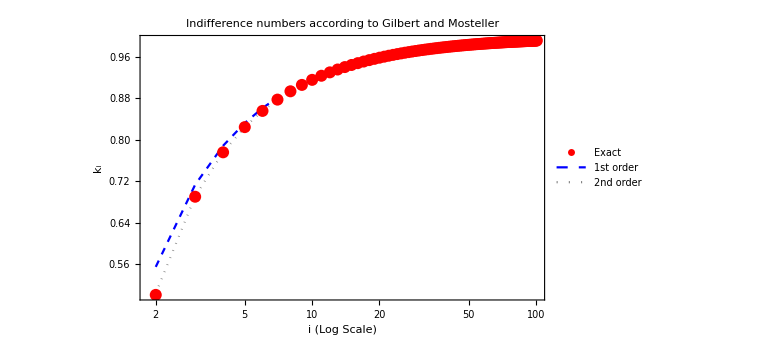

```mathematica
ListPlot[Map[Rest,{kGM,kGM1o,kGM2o}],Frame->True,PlotRange->All,ScalingFunctions->{"Log",None},PlotStyle->{{PointSize[0.015],Red},{Blue,Dashed},{Gray,Dotted}},Joined->{False,True,True},ImageSize->Large,PlotLegends->{"Exact","1st order","2nd order"},PlotLabel->"Indifference numbers according to Gilbert and Mosteller",FrameLabel->{"i (Log Scale)","k_i"}]
```

```mathematica
pmnirall[r1_,d_,n_]:=Module[{r},r=r1-1;
If[r1==1,(1-d⟦1⟧^n)/n,{Table[(d⟦i⟧^r/(r(n-r))),{i,1,r}],Table[-(d⟦i⟧^n/(n(n-r))),{i,1,r}],-d⟦r1⟧^n/n}]];
```

Equations 3 and 4:

```mathematica
pmnir[r1_,d_,n_]:=Module[{r},r=r1-1;
If[r1==1,(1-d⟦1⟧^n)/n,∑_(i=1)^r (d⟦i⟧^r/(r(n-r)))-∑_(i=1)^r (d⟦i⟧^n/(n(n-r)))-d⟦r1⟧^n/n]];
```

```mathematica
pmnit[d_,n_]:=Table[pmnir[r1,d,n],{r1,1,n}];
```

Equation 5:

```mathematica
pmni[d_,n_]:=Sum[pmnir[r1,d,n],{r1,1,n}];
```

```mathematica
getkGM[n_]:=Reverse[Take[Last[Transpose[kGM]],n]];
```

```mathematica
pwinGM[n_]:=pmni[getkGM[n],n];
```

The table of win probabilities using the indifference numbers for 2 to 100 remaining rounds (Table 2):

```mathematica
pwGMtbl=Table[{n,pwinGM[n]},{n,2,100}];
```

```mathematica
TableForm[pwGMtbl]
```

2 | 0.75
3 | 0.684293
4 | 0.655396
5 | 0.639194
6 | 0.628784
7 | 0.621508
8 | 0.616128
9 | 0.611986
10 | 0.608699
11 | 0.606028
12 | 0.603813
13 | 0.601948
14 | 0.600356
15 | 0.59898
16 | 0.59778
17 | 0.596724
18 | 0.595788
19 | 0.594952
20 | 0.5942
21 | 0.593522
22 | 0.592906
23 | 0.592344
24 | 0.59183
25 | 0.591357
26 | 0.590921
27 | 0.590518
28 | 0.590144
29 | 0.589796
30 | 0.589472
31 | 0.589168
32 | 0.588884
33 | 0.588618
34 | 0.588367
35 | 0.58813
36 | 0.587907
37 | 0.587696
38 | 0.587496
39 | 0.587306
40 | 0.587126
41 | 0.586955
42 | 0.586792
43 | 0.586637
44 | 0.586489
45 | 0.586347
46 | 0.586212
47 | 0.586083
48 | 0.585958
49 | 0.585839
50 | 0.585725
51 | 0.585615
52 | 0.58551
53 | 0.585409
54 | 0.585311
55 | 0.585217
56 | 0.585126
57 | 0.585039
58 | 0.584954
59 | 0.584872
60 | 0.584794
61 | 0.584717
62 | 0.584643
63 | 0.584572
64 | 0.584503
65 | 0.584436
66 | 0.584371
67 | 0.584308
68 | 0.584246
69 | 0.584187
70 | 0.584129
71 | 0.584073
72 | 0.584019
73 | 0.583966
74 | 0.583914
75 | 0.583864
76 | 0.583815
77 | 0.583767
78 | 0.583721
79 | 0.583676
80 | 0.583632
81 | 0.583589
82 | 0.583547
83 | 0.583506
84 | 0.583466
85 | 0.583427
86 | 0.583389
87 | 0.583352
88 | 0.583315
89 | 0.58328
90 | 0.583245
91 | 0.583211
92 | 0.583178
93 | 0.583145
94 | 0.583113
95 | 0.583082
96 | 0.583052
97 | 0.583022
98 | 0.582993
99 | 0.582964
100 | 0.582936

Figure 2:

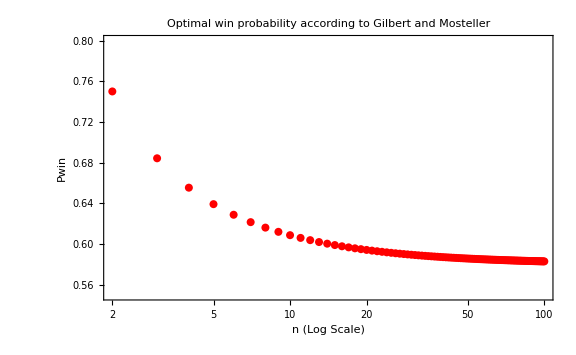

```mathematica
ListPlot[pwGMtbl,Frame->True,PlotRange->{All,{0.55,0.8}},ScalingFunctions->{"Log",None},PlotStyle->{{PointSize[0.01],Red}},ImageSize->Large,PlotLabel->"Optimal win probability according to Gilbert and Mosteller",FrameLabel->{"n (Log Scale)","Pwin"},AxesOrigin->{2,0.58}]
```

The naive strategy (Equation 6):

```mathematica
knaive=Table[{j+1,1-1/(j+1)},{j,0,100}];
```

Figure 3:

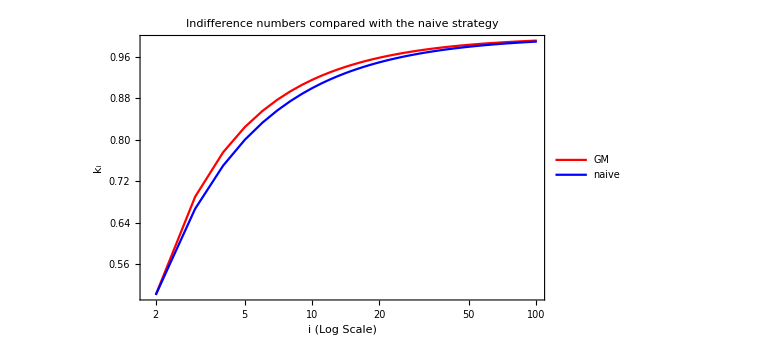

```mathematica
ListLinePlot[Map[Rest,{kGM,knaive}],Frame->True,PlotRange->All,ScalingFunctions->{"Log",None},PlotStyle->{Red,Blue},ImageSize->Large,PlotLegends->{"GM","naive"},PlotLabel->"Indifference numbers compared with the naive strategy",FrameLabel->{"i (Log Scale)","k_i"}]
```

```mathematica
getknaive[n_]:=Reverse[Take[Last[Transpose[knaive]],n]];
```

```mathematica
pwinnaive[n_]:=pmni[getknaive[n],n];
```

```mathematica
pwnaivetbl=Table[{n,pwinnaive[n]},{n,2,100}];
```

```mathematica
pwintGM[n_]:=pmnit[getkGM[n],n];
```

```mathematica
pwtGMtbl=Table[{n,pwintGM[n]},{n,2,100}];
```

```mathematica
pwintnaive[n_]:=pmnit[getknaive[n],n];
```

```mathematica
pwtnaivetbl=Table[{n,pwintnaive[n]},{n,2,100}];
```

Figure 4:

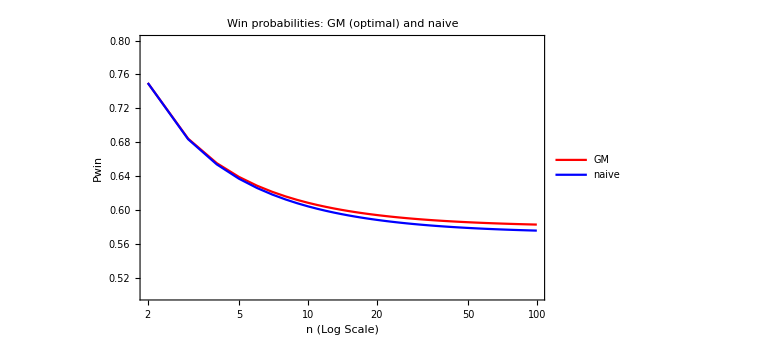

```mathematica
ListLinePlot[{pwGMtbl,pwnaivetbl},Frame->True,PlotRange->{All,{0.5,0.8}},ScalingFunctions->{"Log",None},PlotStyle->{Red,Blue},ImageSize->Large,PlotLabel->"Win probabilities: GM (optimal) and naive",FrameLabel->{"n (Log Scale)","Pwin"},AxesOrigin->{2,0.58},PlotLegends->{"GM","naive"}]
```

Single decision number k for n rounds:

```mathematica
pmnikk[n_,k_]:=pmni[ConstantArray[k,n],n];
```

Figure 5:

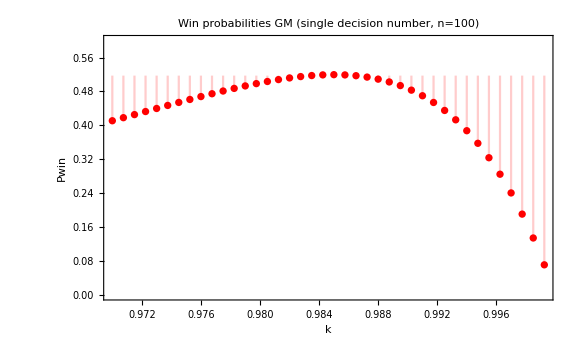

```mathematica
DiscretePlot[pmnikk[100,k],{k,1-2 1.5/100,1-0.01 1.5/100,0.05 1.5/100},Frame->True,PlotRange->{All,{0,0.6}},AxesOrigin->{1-1.5/100,0.51735},ImageSize->Large,PlotStyle->{Red},PlotLabel->"Win probabilities GM (single decision number, n=100)",FrameLabel->{"k","Pwin"}]
```

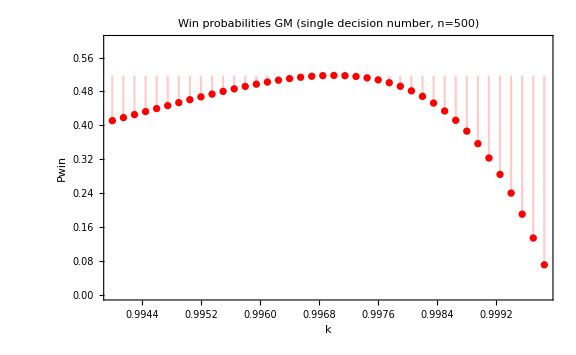

```mathematica
DiscretePlot[pmnikk[500,k],{k,1-2 1.5/500,1-0.01 1.5/500,0.05 1.5/500},Frame->True,PlotRange->{All,{0,0.6}},AxesOrigin->{1-1.5/500,0.51735},ImageSize->Large,PlotStyle->{Red},PlotLabel->"Win probabilities GM (single decision number, n=500)",FrameLabel->{"k","Pwin"}]
```

Single decision number k for t rounds followed by 0 in the last n-t rounds:

```mathematica
pmnikkt[n_,k_,t_]:=pmni[Join[ConstantArray[k,t],ConstantArray[0,n-t]],n];
```

```mathematica
TableForm[Take[Sort[Flatten[Table[{t,k,pmnikkt[100,k,t]},{k,1-2 1/100,1-0.01 1/100,0.05 1/100},{t,30,90,5}],1],#1[[3]]>#2[[3]]&],20]]
```

65 | 0.9885 | 0.56664
65 | 0.988 | 0.566587
65 | 0.989 | 0.566126
65 | 0.9875 | 0.566009
60 | 0.9885 | 0.565475
60 | 0.989 | 0.565395
70 | 0.988 | 0.565265
70 | 0.9875 | 0.565101
60 | 0.988 | 0.565028
65 | 0.9895 | 0.564999
65 | 0.987 | 0.564947
70 | 0.9885 | 0.564867
60 | 0.9895 | 0.564745
70 | 0.987 | 0.564419
60 | 0.9875 | 0.564092
70 | 0.989 | 0.563862
60 | 0.99 | 0.563479
65 | 0.9865 | 0.563437
70 | 0.9865 | 0.563257
65 | 0.99 | 0.563213

```mathematica
TableForm[Take[Sort[Flatten[Table[{t,k,pmnikkt[100,k,t]},{k,1-2 1/100,1-0.01 1/100,0.05 1/100},{t,60,70,1}],1],#1[[3]]>#2[[3]]&],20]]
```

64 | 0.9885 | 0.566651
65 | 0.9885 | 0.56664
65 | 0.988 | 0.566587
66 | 0.988 | 0.566544
63 | 0.9885 | 0.566543
64 | 0.988 | 0.566515
66 | 0.9885 | 0.566512
67 | 0.988 | 0.566389
63 | 0.988 | 0.566325
62 | 0.9885 | 0.566312
67 | 0.9885 | 0.566268
64 | 0.989 | 0.566228
63 | 0.989 | 0.566209
65 | 0.989 | 0.566126
68 | 0.988 | 0.566122
62 | 0.989 | 0.566065
66 | 0.9875 | 0.566045
62 | 0.988 | 0.566016
65 | 0.9875 | 0.566009
67 | 0.9875 | 0.56597

```mathematica
N[{1/(1+1.17/100),1-2 1/100,1-0.01 1/100,0.05 1/100}]
```

{0.988435,0.98,0.9999,0.0005}

```mathematica
TableForm[Take[Sort[Flatten[Table[{t,k,pmnikkt[100,k,t]},{k,0.9882,0.9884,0.00001},{t,60,70,1}],1],#1[[3]]>#2[[3]]&],20]]
```

65 | 0.9883 | 0.566684
65 | 0.98831 | 0.566684
65 | 0.98829 | 0.566684
65 | 0.98832 | 0.566684
65 | 0.98828 | 0.566684
65 | 0.98833 | 0.566684
65 | 0.98827 | 0.566683
65 | 0.98834 | 0.566683
65 | 0.98826 | 0.566683
65 | 0.98835 | 0.566682
65 | 0.98825 | 0.566682
65 | 0.98836 | 0.566681
65 | 0.98824 | 0.566681
65 | 0.98823 | 0.566679
65 | 0.98837 | 0.566679
65 | 0.98822 | 0.566677
65 | 0.98838 | 0.566677
65 | 0.98821 | 0.566676
65 | 0.98839 | 0.566676
65 | 0.9882 | 0.566674

Asymptotic probability of winning at round i:

```mathematica
pwtGMtblnP=Table[Transpose[{Range[n]/n,n pwintGM[n]}],{n,2,100}];
```

Figure 6:

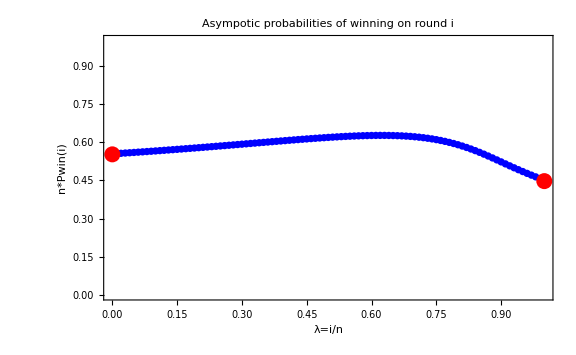

```mathematica
ListPlot[
Last[pwtGMtblnP],
Epilog->{
Red,PointSize[0.02],Point[{0,1-ⅇ^-c}],
Red,PointSize[0.02],Point[{1,ⅇ^-c}]},
Frame->True,PlotRange->{All,{0,1}},PlotLabel->"Asympotic probabilities of winning on round i",
FrameLabel->{"λ=i/n","n*Pwin(i)"},ImageSize->Large,PlotStyle->Blue]
```

## 2. Visualization

n = 2

Figure 7:

```mathematica
rplot[k1_]:=RegionPlot[{
k1≤a1≤1&&a1≥a2,
k1≤a1≤1&&a1<a2,
0≤a1<k1&&a1≥a2,
0≤a1<k1&&a1<a2},
{a1,0,1},{a2,0,1},
AspectRatio->1,ImageSize->Medium,Frame->True,PlotStyle->{Red,Brown,Blue,Yellow},
PlotLabel->StringJoin["n=2, k_1=",ToString[k1]],
FrameLabel->{"First number drawn - a_1","Last number drawn - a_2"},PlotLegends->{"1: wins (on the 1st round)","2: loses (False Positive)","3: loses (False Negative)","4: continues (to win on the 2nd round)"}];
```

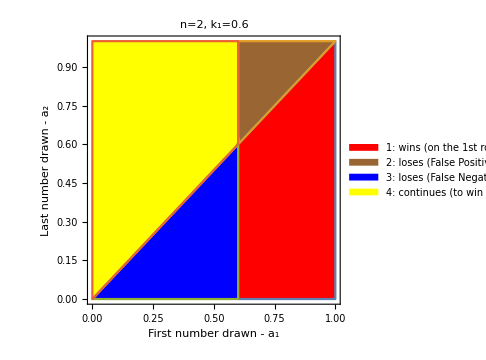

```mathematica
rplot[0.6]
```

n = 3

Figure 8:

```mathematica
RegionPlot3D[
a1==Max[a1,a2,a3],
{a2,0,1},{a3,0,1},{a1,0,1},
ImageSize->Large,PlotStyle->{Red},BoxRatios->{1,1,1},
PlotLabel->"n=3, a_1=Max(a_j)",
AxesLabel->{"Second number drawn - a_2","Last number drawn - a_3","First number drawn - a_1"}]
```

-Graphics3D-

Figures 9a,b,c:

```mathematica
rplot3w1[k1_]:=RegionPlot3D[
k1≤a1≤1&&a1==Max[a1,a2,a3],
{a2,0,1},{a3,0,1},{a1,0,1},
ImageSize->Medium,PlotStyle->{Red},BoxRatios->{1,1,1},
PlotLabel->StringJoin["n=3, k_1=",ToString[k1],"; 1: wins (on the 1st round)"],
AxesLabel->{"a_2","a_3","a_1"},MaxRecursion->100];
```

```mathematica
rplot3w1[0.6]
```

-Graphics3D-

```mathematica
rplot3l1fp[k1_]:=RegionPlot3D[
k1≤a1≤1&&a1<Max[a1,a2,a3],
{a2,0,1},{a3,0,1},{a1,0,1},
ImageSize->Medium,PlotStyle->{Brown},BoxRatios->{1,1,1},
PlotLabel->StringJoin["n=3, k_1=",ToString[k1],"; 2: loses (False Positive)"],
AxesLabel->{"a_2","a_3","a_1"},MaxRecursion->100];
```

```mathematica
rplot3l1fp[0.6]
```

-Graphics3D-

```mathematica
rplot3l1fn[k1_]:=RegionPlot3D[
0≤a1<k1&&a1==Max[a1,a2,a3],
{a2,0,1},{a3,0,1},{a1,0,1},
ImageSize->Medium,PlotStyle->{Blue},BoxRatios->{1,1,1},
PlotLabel->StringJoin["n=3, k_1=",ToString[k1],"; 3: loses (False Negative)"],
AxesLabel->{"a_2","a_3","a_1"},MaxRecursion->100];
```

```mathematica
rplot3l1fn[0.6]
```

-Graphics3D-

Figure 10:

```mathematica
rplot3c1[k1_]:=RegionPlot3D[
0≤a1<k1&&a1<Max[a1,a2,a3],
{a2,0,1},{a3,0,1},{a1,0,1},
ImageSize->Medium,PlotStyle->{Yellow},BoxRatios->{1,1,1},
PlotLabel->StringJoin["n=3, k_1=",ToString[k1],"; 4: continues (to the 2nd round)"],
AxesLabel->{"a_2","a_3","a_1"},MaxRecursion->100];
```

```mathematica
rplot3c1[0.6]
```

-Graphics3D-

Figure 11:

```mathematica
rplot3to2[k1_,a1_]:=RegionPlot[{
k1≤a2≤1&&a2≥a3,
k1≤a2≤1&&a2<a3,
a1≤a2<k1&&a2≥a3,
a1≤a3<1&&0≤a2<k1&&a2<a3,
0≤a3<a1&&0≤a2<a1},
{a2,0,1},{a3,0,1},
AspectRatio->1,ImageSize->Medium,Frame->True,PlotStyle->{Red,Brown,Blue,Yellow,Black},
PlotLabel->StringJoin["n=3, k_1=",ToString[k1],", a_1=",ToString[a1]],
FrameLabel->{"Second number drawn - a_2","Last number drawn - a_3"},PlotLegends->{"1: wins (on the 2nd round)","2: loses (False Positive)","3: loses (False Negative)","4: continues (to win on the 3rd round)","5: cut out (False negative from 1st round)"}];
```

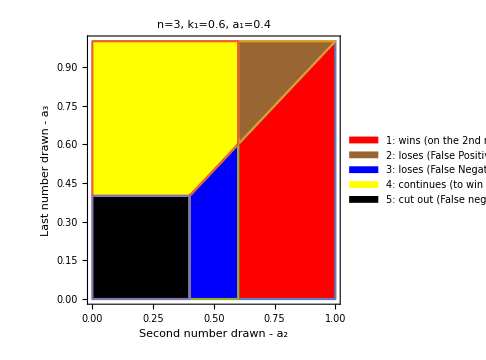

```mathematica
rplot3to2[0.6,0.4]
```

Figures 12a,b,c:

```mathematica
rplot3w2[k1_,k2_]:=RegionPlot3D[
k2≤a2≤1&&a2==Max[a1,a2,a3]&&0≤a1<k1&&a1<Max[a1,a2,a3],
{a2,0,1},{a3,0,1},{a1,0,1},
ImageSize->Medium,PlotStyle->{Red},BoxRatios->{1,1,1},
PlotLabel->StringJoin["n=3, k_1=",ToString[k1],", k_2=",ToString[k2],"; 1: wins (on the 2nd round)"],
AxesLabel->{"a_2","a_3","a_1"},MaxRecursion->100];
```

```mathematica
rplot3w2[0.6,0.4]
```

-Graphics3D-

```mathematica
rplot3l2fp[k1_,k2_]:=RegionPlot3D[
k2≤a2≤1&&a2<Max[a1,a2,a3]&&0≤a1<k1&&a1<Max[a1,a2,a3],
{a2,0,1},{a3,0,1},{a1,0,1},
ImageSize->Medium,PlotStyle->{Brown},BoxRatios->{1,1,1},
PlotLabel->StringJoin["n=3, k_1=",ToString[k1],", k_2=",ToString[k2],"; 2: loses (False Positive)"],
AxesLabel->{"a_2","a_3","a_1"},MaxRecursion->100];
```

```mathematica
rplot3l2fp[0.6,0.4]
```

-Graphics3D-

```mathematica
rplot3l2fn[k1_,k2_]:=RegionPlot3D[
0≤a2≤k2&&a2==Max[a1,a2,a3]&&0≤a1<k1&&a1<Max[a1,a2,a3],
{a2,0,1},{a3,0,1},{a1,0,1},
ImageSize->Medium,PlotStyle->{Blue},BoxRatios->{1,1,1},
PlotLabel->StringJoin["n=3, k_1=",ToString[k1],", k_2=",ToString[k2],"; 3: loses (False Negative))"],
AxesLabel->{"a_2","a_3","a_1"},MaxRecursion->100];
```

```mathematica
rplot3l2fn[0.6,0.4]
```

-Graphics3D-

Figure 13:

```mathematica
rplot3c2[k1_,k2_]:=RegionPlot3D[
0≤a2≤k2&&a2<Max[a1,a2,a3]&&0≤a1<k1&&a1<Max[a1,a2,a3],
{a2,0,1},{a3,0,1},{a1,0,1},
ImageSize->Medium,PlotStyle->{Yellow},BoxRatios->{1,1,1},
PlotLabel->StringJoin["n=3, k_1=",ToString[k1],", k_2=",ToString[k2],"; 4: continues (to win on the 3rd round)"],
AxesLabel->{"a_2","a_3","a_1"},MaxRecursion->100];
```

```mathematica
rplot3c2[0.6,0.4]
```

-Graphics3D-

## 3. Integration

```mathematica
probs[n_,conds_,assumps_]:=Module[{vars,dists},
vars=Table[Subscript[a, j],{j,1,n}];
dists=Table[Subscript[a, j]\[Distributed]UniformDistribution[],{j,1,n}];
FullSimplify[Assuming[assumps,Probability[conds,dists]]]];
```

```mathematica
probnrk[n_,r_,k_,ak_:True,amax_:True,fak_:GreaterEqual,famax_:GreaterEqual,andorcond_:And]:=Module[{vars,maxv,varsp,maxp,cutsp,ksymb,assumps,compsp,compsmaxp,compr,compmaxr,condsp,condsr,conds,ans},
vars=Table[Subscript[a, j],{j,1,n}];
maxv=Apply[Max,vars];
varsp=Table[Subscript[a, j],{j,1,r-1}];
maxp=If[r>1,Apply[Max,varsp],0];
cutsp=Take[k,r-1];
ksymb=Union[Select[k,Not[NumberQ[#]]&]];
assumps=Apply[And,Append[Map[(0<#<1)&,ksymb],(0<x≤1)]];
compsp=MapThread[(#1<#2)&,{varsp,cutsp}];
compsmaxp={maxp<maxv};
If[ak,compr=fak[vars⟦r⟧,k⟦r⟧],compr=True];
If[amax,compmaxr=famax[vars⟦r⟧,maxv],compmaxr=True];
condsp=Apply[And,Join[compsp,compsmaxp]];
condsr=And[compr,compmaxr];
conds=andorcond[condsr,condsp];
ans=probs[n,conds,assumps];
Expand[ans]];
```

```mathematica
probnrkall[n_,r_,k_,ak_:True,amax_:True,fak_:GreaterEqual,famax_:GreaterEqual,andorcond_:And]:=Module[{vars,maxv,varsp,maxp,cutsp,ksymb,assumps,compsp,compsmaxp,compr,compmaxr,condsp,condsr,conds,ans},
vars=Table[Subscript[a, j],{j,1,n}];
maxv=Apply[Max,vars];
varsp=Table[Subscript[a, j],{j,1,r-1}];
maxp=If[r>1,Apply[Max,varsp],0];
cutsp=Take[k,r-1];
ksymb=Union[Select[k,Not[NumberQ[#]]&]];
assumps=Apply[And,Append[Map[(0<#<1)&,ksymb],(0<x≤1)]];
compsp=MapThread[(#1<#2)&,{varsp,cutsp}];
compsmaxp={maxp<maxv};
If[ak,compr=fak[vars⟦r⟧,k⟦r⟧],compr=True];
If[amax,compmaxr=famax[vars⟦r⟧,maxv],compmaxr=True];
condsp=Apply[And,Join[compsp,compsmaxp]];
condsr=And[compr,compmaxr];
conds=andorcond[condsr,condsp];
ans=probs[n,conds,assumps];
{conds,assumps,Expand[ans]}];
```

```mathematica
grid={{GreaterEqual,GreaterEqual},{GreaterEqual,Less},{Less,GreaterEqual},{Less,Less}};
```

```mathematica
Grid[Expand[Map[probnrkall[2,1,{Subscript[k, 1],0},True,True,#⟦1⟧,#⟦2⟧]&,grid]],Frame->All]
```

a_1≥k_1&&a_1≥Max[a_1,a_2]&&0<Max[a_1,a_2] | 0<k_1<1&&0<x≤1 | 1/2-k_1^2/2
a_1≥k_1&&a_1<Max[a_1,a_2]&&0<Max[a_1,a_2] | 0<k_1<1&&0<x≤1 | 1/2-k_1+k_1^2/2
a_1<k_1&&a_1≥Max[a_1,a_2]&&0<Max[a_1,a_2] | 0<k_1<1&&0<x≤1 | k_1^2/2
a_1<k_1&&a_1<Max[a_1,a_2]&&0<Max[a_1,a_2] | 0<k_1<1&&0<x≤1 | k_1-k_1^2/2

```mathematica
Grid[Expand[Map[probnrkall[2,2,{Subscript[k, 1],0},True,True,#⟦1⟧,#⟦2⟧]&,grid]],Frame->All]
```

a_2≥0&&a_2≥Max[a_1,a_2]&&a_1<k_1&&a_1<Max[a_1,a_2] | 0<k_1<1&&0<x≤1 | k_1-k_1^2/2
a_2≥0&&a_2<Max[a_1,a_2]&&a_1<k_1&&a_1<Max[a_1,a_2] | 0<k_1<1&&0<x≤1 | 0
a_2<0&&a_2≥Max[a_1,a_2]&&a_1<k_1&&a_1<Max[a_1,a_2] | 0<k_1<1&&0<x≤1 | 0
a_2<0&&a_2<Max[a_1,a_2]&&a_1<k_1&&a_1<Max[a_1,a_2] | 0<k_1<1&&0<x≤1 | 0

```mathematica
TableForm[Expand[pmnit[{Subscript[k, 1],0},2]]]
```

1/2-k_1^2/2
k_1-k_1^2/2

```mathematica
Assuming[Subscript[k, 1]>Subscript[k, 2],Grid[Expand[Map[probnrkall[2,2,{Subscript[k, 1],Subscript[k, 2]},True,True,#⟦1⟧,#⟦2⟧]&,grid]],Frame->All]]
```

a_2≥k_2&&a_2≥Max[a_1,a_2]&&a_1<k_1&&a_1<Max[a_1,a_2] | 0<k_1<1&&0<k_2<1&&0<x≤1 | k_1-k_1^2/2-k_2^2/2
a_2≥k_2&&a_2<Max[a_1,a_2]&&a_1<k_1&&a_1<Max[a_1,a_2] | 0<k_1<1&&0<k_2<1&&0<x≤1 | 0
a_2<k_2&&a_2≥Max[a_1,a_2]&&a_1<k_1&&a_1<Max[a_1,a_2] | 0<k_1<1&&0<k_2<1&&0<x≤1 | k_2^2/2
a_2<k_2&&a_2<Max[a_1,a_2]&&a_1<k_1&&a_1<Max[a_1,a_2] | 0<k_1<1&&0<k_2<1&&0<x≤1 | 0

```mathematica
TableForm[Expand[pmnit[{Subscript[k, 1],Subscript[k, 2]},2]]]
```

1/2-k_1^2/2
k_1-k_1^2/2-k_2^2/2

```mathematica
Grid[Expand[Map[probnrkall[3,1,{Subscript[k, 1],Subscript[k, 2],0},True,True,#⟦1⟧,#⟦2⟧]&,grid]],Frame->All]
```

a_1≥k_1&&a_1≥Max[a_1,a_2,a_3]&&0<Max[a_1,a_2,a_3] | 0<k_1<1&&0<k_2<1&&0<x≤1 | 1/3-k_1^3/3
a_1≥k_1&&a_1<Max[a_1,a_2,a_3]&&0<Max[a_1,a_2,a_3] | 0<k_1<1&&0<k_2<1&&0<x≤1 | 2/3-k_1+k_1^3/3
a_1<k_1&&a_1≥Max[a_1,a_2,a_3]&&0<Max[a_1,a_2,a_3] | 0<k_1<1&&0<k_2<1&&0<x≤1 | k_1^3/3
a_1<k_1&&a_1<Max[a_1,a_2,a_3]&&0<Max[a_1,a_2,a_3] | 0<k_1<1&&0<k_2<1&&0<x≤1 | k_1-k_1^3/3

```mathematica
Assuming[Subscript[k, 1]>Subscript[k, 2],Grid[Expand[Map[probnrkall[3,2,{Subscript[k, 1],Subscript[k, 2],0},True,True,#⟦1⟧,#⟦2⟧]&,grid]],Frame->All]]
```

a_2≥k_2&&a_2≥Max[a_1,a_2,a_3]&&a_1<k_1&&a_1<Max[a_1,a_2,a_3] | 0<k_1<1&&0<k_2<1&&0<x≤1 | k_1/2-k_1^3/6-k_2^3/3
a_2≥k_2&&a_2<Max[a_1,a_2,a_3]&&a_1<k_1&&a_1<Max[a_1,a_2,a_3] | 0<k_1<1&&0<k_2<1&&0<x≤1 | k_1/2-k_1^3/6-k_1 k_2+1/2 k_1^2 k_2+k_2^3/6
a_2<k_2&&a_2≥Max[a_1,a_2,a_3]&&a_1<k_1&&a_1<Max[a_1,a_2,a_3] | 0<k_1<1&&0<k_2<1&&0<x≤1 | k_2^3/3
a_2<k_2&&a_2<Max[a_1,a_2,a_3]&&a_1<k_1&&a_1<Max[a_1,a_2,a_3] | 0<k_1<1&&0<k_2<1&&0<x≤1 | k_1 k_2-1/2 k_1^2 k_2-k_2^3/6

```mathematica
Grid[Expand[Map[probnrkall[3,2,{k,k,0},True,True,#⟦1⟧,#⟦2⟧]&,grid]],Frame->All]
```

a_2≥k&&a_2≥Max[a_1,a_2,a_3]&&a_1<k&&a_1<Max[a_1,a_2,a_3] | 0<k<1&&0<x≤1 | k/2-k^3/2
a_2≥k&&a_2<Max[a_1,a_2,a_3]&&a_1<k&&a_1<Max[a_1,a_2,a_3] | 0<k<1&&0<x≤1 | k/2-k^2+k^3/2
a_2<k&&a_2≥Max[a_1,a_2,a_3]&&a_1<k&&a_1<Max[a_1,a_2,a_3] | 0<k<1&&0<x≤1 | k^3/3
a_2<k&&a_2<Max[a_1,a_2,a_3]&&a_1<k&&a_1<Max[a_1,a_2,a_3] | 0<k<1&&0<x≤1 | k^2-(2 k^3)/3

```mathematica
Assuming[Subscript[k, 1]>Subscript[k, 2],Grid[Expand[Map[probnrkall[3,3,{Subscript[k, 1],Subscript[k, 2],0},True,True,#⟦1⟧,#⟦2⟧]&,grid]],Frame->All]]
```

a_3≥0&&a_3≥Max[a_1,a_2,a_3]&&a_1<k_1&&a_2<k_2&&Max[a_1,a_2]<Max[a_1,a_2,a_3] | 0<k_1<1&&0<k_2<1&&0<x≤1 | k_1 k_2-1/2 k_1^2 k_2-k_2^3/6
a_3≥0&&a_3<Max[a_1,a_2,a_3]&&a_1<k_1&&a_2<k_2&&Max[a_1,a_2]<Max[a_1,a_2,a_3] | 0<k_1<1&&0<k_2<1&&0<x≤1 | 0
a_3<0&&a_3≥Max[a_1,a_2,a_3]&&a_1<k_1&&a_2<k_2&&Max[a_1,a_2]<Max[a_1,a_2,a_3] | 0<k_1<1&&0<k_2<1&&0<x≤1 | 0
a_3<0&&a_3<Max[a_1,a_2,a_3]&&a_1<k_1&&a_2<k_2&&Max[a_1,a_2]<Max[a_1,a_2,a_3] | 0<k_1<1&&0<k_2<1&&0<x≤1 | 0

```mathematica
Grid[Expand[Map[probnrkall[3,3,{k,k,0},True,True,#⟦1⟧,#⟦2⟧]&,grid]],Frame->All]
```

a_3≥0&&a_3≥Max[a_1,a_2,a_3]&&a_1<k&&a_2<k&&Max[a_1,a_2]<Max[a_1,a_2,a_3] | 0<k<1&&0<x≤1 | k^2-(2 k^3)/3
a_3≥0&&a_3<Max[a_1,a_2,a_3]&&a_1<k&&a_2<k&&Max[a_1,a_2]<Max[a_1,a_2,a_3] | 0<k<1&&0<x≤1 | 0
a_3<0&&a_3≥Max[a_1,a_2,a_3]&&a_1<k&&a_2<k&&Max[a_1,a_2]<Max[a_1,a_2,a_3] | 0<k<1&&0<x≤1 | 0
a_3<0&&a_3<Max[a_1,a_2,a_3]&&a_1<k&&a_2<k&&Max[a_1,a_2]<Max[a_1,a_2,a_3] | 0<k<1&&0<x≤1 | 0

```mathematica
TableForm[Expand[pmnit[{Subscript[k, 1],Subscript[k, 2],0},3]]]
```

1/3-k_1^3/3
k_1/2-k_1^3/6-k_2^3/3
k_1^2/2-k_1^3/3+k_2^2/2-k_2^3/3

```mathematica
TableForm[Expand[pmnit[{k,k,0},3]]]
```

1/3-k^3/3
k/2-k^3/2
k^2-(2 k^3)/3

```mathematica
Grid[{Assuming[Subscript[k, 1]>Subscript[k, 2],probnrkall[3,3,{Subscript[k, 1],Subscript[k, 2],0},True,True,GreaterEqual,GreaterEqual]]},Frame->All]
```

a_3≥0&&a_3≥Max[a_1,a_2,a_3]&&a_1<k_1&&a_2<k_2&&Max[a_1,a_2]<Max[a_1,a_2,a_3] | 0<k_1<1&&0<k_2<1&&0<x≤1 | k_1 k_2-1/2 k_1^2 k_2-k_2^3/6

```mathematica
Assuming[Subscript[k, 1]>Subscript[k, 2],Expand[probs[3,
Subscript[a, 3]≥0&&Subscript[a, 3]≥Max[Subscript[a, 1],Subscript[a, 2],Subscript[a, 3]]&&Subscript[a, 1]<Subscript[k, 1]&&Subscript[a, 2]<Subscript[k, 2]&&Max[Subscript[a, 1],Subscript[a, 2]]<Max[Subscript[a, 1],Subscript[a, 2],Subscript[a, 3]],
0<Subscript[k, 1]<1&&0<Subscript[k, 2]<1&&0<x≤1]]]
```

k_1 k_2-1/2 k_1^2 k_2-k_2^3/6

```mathematica
Assuming[Subscript[k, 1]>Subscript[k, 2],Expand[probs[3,
Subscript[a, 3]≥0&&Subscript[a, 3]≥Max[Subscript[a, 1],Subscript[a, 2],Subscript[a, 3]]&&((Subscript[a, 1]<Subscript[k, 1])&&Max[Subscript[a, 1],Subscript[a, 2]]<Max[Subscript[a, 1],Subscript[a, 2],Subscript[a, 3]]),
0<Subscript[k, 1]<1&&0<Subscript[k, 2]<1&&0<x≤1]]]
```

k_1/2-k_1^3/6

```mathematica
Assuming[Subscript[k, 1]>Subscript[k, 2],Expand[probs[3,
Subscript[a, 3]≥0&&Subscript[a, 3]≥Max[Subscript[a, 1],Subscript[a, 2],Subscript[a, 3]]&&((Subscript[a, 2]<Subscript[k, 2])&&Max[Subscript[a, 1],Subscript[a, 2]]<Max[Subscript[a, 1],Subscript[a, 2],Subscript[a, 3]]),
0<Subscript[k, 1]<1&&0<Subscript[k, 2]<1&&0<x≤1]]]
```

k_2/2-k_2^3/6

```mathematica
TableForm[Expand[pmnit[{Subscript[k, 1],Subscript[k, 2],Subscript[k, 3],0},4]]]
```

1/4-k_1^4/4
k_1/3-k_1^4/12-k_2^4/4
k_1^2/4-k_1^4/8+k_2^2/4-k_2^4/8-k_3^4/4
k_1^3/3-k_1^4/4+k_2^3/3-k_2^4/4+k_3^3/3-k_3^4/4

Equation 8

```mathematica
Assuming[Subscript[k, 1]>Subscript[k, 2],Sum[probnrk[3,r,{Subscript[k, 1],Subscript[k, 2],0},True,True,GreaterEqual,GreaterEqual],{r,1,3}]]
```

1/3+k_1/2-k_1^3/2+k_1 k_2-1/2 k_1^2 k_2-k_2^3/2

```mathematica
NMaximize[{1/3+Subscript[k, 1]/2-Subscript[k, 1]^3/2+Subscript[k, 1] Subscript[k, 2]-1/2 Subscript[k, 1]^2 Subscript[k, 2]-Subscript[k, 2]^3/2,0<Subscript[k, 1]<1&&0<Subscript[k, 2]<1},{Subscript[k, 1],Subscript[k, 2]}]
```

{0.679846,{k_1→0.672608,k_2→0.545532}}

```mathematica
(1/3+Subscript[k, 1]/2-Subscript[k, 1]^3/2+Subscript[k, 1] Subscript[k, 2]-1/2 Subscript[k, 1]^2 Subscript[k, 2]-Subscript[k, 2]^3/2)//.{Subscript[k, 1]->0.684293,Subscript[k, 2]->0.5}
```

0.67785

## 4. Generalization

```mathematica
Timing[tables=Assuming[Subscript[k, 1]>Subscript[k, 2]>Subscript[k, 3]>Subscript[k, 4]>Subscript[k, 5],Table[Map[probnrk[n,r,Append[Table[Subscript[k, i],{i,1,n-1}],0],True,True,#⟦1⟧,#⟦2⟧]&,grid],{n,2,5},{r,1,n}]];]
```

{152.292,Null}

```mathematica
Timing[tables6=Assuming[Subscript[k, 1]>Subscript[k, 2]>Subscript[k, 3]>Subscript[k, 4]>Subscript[k, 5],Table[Map[probnrk[n,r,Append[Table[Subscript[k, i],{i,1,n-1}],0],True,True,#⟦1⟧,#⟦2⟧]&,grid],{n,2,6},{r,1,n}]];]
```

{4727.54,Null}

```mathematica
TableForm[Map[{Grid[#,Frame->All]}&,tables]]
```

1/2-k_1^2/2 | 1/2-k_1+k_1^2/2 | k_1^2/2 | k_1-k_1^2/2
k_1-k_1^2/2 | 0 | 0 | 0
1/3-k_1^3/3 | 2/3-k_1+k_1^3/3 | k_1^3/3 | k_1-k_1^3/3
k_1/2-k_1^3/6-k_2^3/3 | k_1/2-k_1^3/6-k_1 k_2+1/2 k_1^2 k_2+k_2^3/6 | k_2^3/3 | k_1 k_2-1/2 k_1^2 k_2-k_2^3/6
k_1 k_2-1/2 k_1^2 k_2-k_2^3/6 | 0 | 0 | 0
1/4-k_1^4/4 | 3/4-k_1+k_1^4/4 | k_1^4/4 | k_1-k_1^4/4
k_1/3-k_1^4/12-k_2^4/4 | (2 k_1)/3-k_1^4/6-k_1 k_2+1/3 k_1^3 k_2+k_2^4/6 | k_2^4/4 | k_1 k_2-1/3 k_1^3 k_2-k_2^4/6
(k_1 k_2)/2-1/6 k_1^3 k_2-k_2^4/12-k_3^4/4 | (k_1 k_2)/2-1/6 k_1^3 k_2-k_2^4/12-k_1 k_2 k_3+1/2 k_1^2 k_2 k_3+1/6 k_2^3 k_3+k_3^4/12 | k_3^4/4 | k_1 k_2 k_3-1/2 k_1^2 k_2 k_3-1/6 k_2^3 k_3-k_3^4/12
k_1 k_2 k_3-1/2 k_1^2 k_2 k_3-1/6 k_2^3 k_3-k_3^4/12 | 0 | 0 | 0
1/5-k_1^5/5 | 4/5-k_1+k_1^5/5 | k_1^5/5 | k_1-k_1^5/5
k_1/4-k_1^5/20-k_2^5/5 | (3 k_1)/4-(3 k_1^5)/20-k_1 k_2+1/4 k_1^4 k_2+(3 k_2^5)/20 | k_2^5/5 | k_1 k_2-1/4 k_1^4 k_2-(3 k_2^5)/20
(k_1 k_2)/3-1/12 k_1^4 k_2-k_2^5/20-k_3^5/5 | (2 k_1 k_2)/3-1/6 k_1^4 k_2-k_2^5/10-k_1 k_2 k_3+1/3 k_1^3 k_2 k_3+1/6 k_2^4 k_3+k_3^5/10 | k_3^5/5 | k_1 k_2 k_3-1/3 k_1^3 k_2 k_3-1/6 k_2^4 k_3-k_3^5/10
1/2 k_1 k_2 k_3-1/6 k_1^3 k_2 k_3-1/12 k_2^4 k_3-k_3^5/20-k_4^5/5 | 1/2 k_1 k_2 k_3-1/6 k_1^3 k_2 k_3-1/12 k_2^4 k_3-k_3^5/20-k_1 k_2 k_3 k_4+1/2 k_1^2 k_2 k_3 k_4+1/6 k_2^3 k_3 k_4+1/12 k_3^4 k_4+k_4^5/20 | k_4^5/5 | k_1 k_2 k_3 k_4-1/2 k_1^2 k_2 k_3 k_4-1/6 k_2^3 k_3 k_4-1/12 k_3^4 k_4-k_4^5/20
k_1 k_2 k_3 k_4-1/2 k_1^2 k_2 k_3 k_4-1/6 k_2^3 k_3 k_4-1/12 k_3^4 k_4-k_4^5/20 | 0 | 0 | 0

```mathematica
TableForm[Map[{Grid[#,Frame->All]}&,tables6]]
```

1/2-k_1^2/2 | 1/2-k_1+k_1^2/2 | k_1^2/2 | k_1-k_1^2/2
k_1-k_1^2/2 | 0 | 0 | 0
1/3-k_1^3/3 | 2/3-k_1+k_1^3/3 | k_1^3/3 | k_1-k_1^3/3
k_1/2-k_1^3/6-k_2^3/3 | k_1/2-k_1^3/6-k_1 k_2+1/2 k_1^2 k_2+k_2^3/6 | k_2^3/3 | k_1 k_2-1/2 k_1^2 k_2-k_2^3/6
k_1 k_2-1/2 k_1^2 k_2-k_2^3/6 | 0 | 0 | 0
1/4-k_1^4/4 | 3/4-k_1+k_1^4/4 | k_1^4/4 | k_1-k_1^4/4
k_1/3-k_1^4/12-k_2^4/4 | (2 k_1)/3-k_1^4/6-k_1 k_2+1/3 k_1^3 k_2+k_2^4/6 | k_2^4/4 | k_1 k_2-1/3 k_1^3 k_2-k_2^4/6
(k_1 k_2)/2-1/6 k_1^3 k_2-k_2^4/12-k_3^4/4 | (k_1 k_2)/2-1/6 k_1^3 k_2-k_2^4/12-k_1 k_2 k_3+1/2 k_1^2 k_2 k_3+1/6 k_2^3 k_3+k_3^4/12 | k_3^4/4 | k_1 k_2 k_3-1/2 k_1^2 k_2 k_3-1/6 k_2^3 k_3-k_3^4/12
k_1 k_2 k_3-1/2 k_1^2 k_2 k_3-1/6 k_2^3 k_3-k_3^4/12 | 0 | 0 | 0
1/5-k_1^5/5 | 4/5-k_1+k_1^5/5 | k_1^5/5 | k_1-k_1^5/5
k_1/4-k_1^5/20-k_2^5/5 | (3 k_1)/4-(3 k_1^5)/20-k_1 k_2+1/4 k_1^4 k_2+(3 k_2^5)/20 | k_2^5/5 | k_1 k_2-1/4 k_1^4 k_2-(3 k_2^5)/20
(k_1 k_2)/3-1/12 k_1^4 k_2-k_2^5/20-k_3^5/5 | (2 k_1 k_2)/3-1/6 k_1^4 k_2-k_2^5/10-k_1 k_2 k_3+1/3 k_1^3 k_2 k_3+1/6 k_2^4 k_3+k_3^5/10 | k_3^5/5 | k_1 k_2 k_3-1/3 k_1^3 k_2 k_3-1/6 k_2^4 k_3-k_3^5/10
1/2 k_1 k_2 k_3-1/6 k_1^3 k_2 k_3-1/12 k_2^4 k_3-k_3^5/20-k_4^5/5 | 1/2 k_1 k_2 k_3-1/6 k_1^3 k_2 k_3-1/12 k_2^4 k_3-k_3^5/20-k_1 k_2 k_3 k_4+1/2 k_1^2 k_2 k_3 k_4+1/6 k_2^3 k_3 k_4+1/12 k_3^4 k_4+k_4^5/20 | k_4^5/5 | k_1 k_2 k_3 k_4-1/2 k_1^2 k_2 k_3 k_4-1/6 k_2^3 k_3 k_4-1/12 k_3^4 k_4-k_4^5/20
k_1 k_2 k_3 k_4-1/2 k_1^2 k_2 k_3 k_4-1/6 k_2^3 k_3 k_4-1/12 k_3^4 k_4-k_4^5/20 | 0 | 0 | 0
1/6-k_1^6/6 | 5/6-k_1+k_1^6/6 | k_1^6/6 | k_1-k_1^6/6
k_1/5-k_1^6/30-k_2^6/6 | (4 k_1)/5-(2 k_1^6)/15-k_1 k_2+1/5 k_1^5 k_2+(2 k_2^6)/15 | k_2^6/6 | k_1 k_2-1/5 k_1^5 k_2-(2 k_2^6)/15
(k_1 k_2)/4-1/20 k_1^5 k_2-k_2^6/30-k_3^6/6 | (3 k_1 k_2)/4-3/20 k_1^5 k_2-k_2^6/10-k_1 k_2 k_3+1/4 k_1^4 k_2 k_3+3/20 k_2^5 k_3+k_3^6/10 | k_3^6/6 | k_1 k_2 k_3-1/4 k_1^4 k_2 k_3-3/20 k_2^5 k_3-k_3^6/10
1/3 k_1 k_2 k_3-1/12 k_1^4 k_2 k_3-1/20 k_2^5 k_3-k_3^6/30-k_4^6/6 | 2/3 k_1 k_2 k_3-1/6 k_1^4 k_2 k_3-1/10 k_2^5 k_3-k_3^6/15-k_1 k_2 k_3 k_4+1/3 k_1^3 k_2 k_3 k_4+1/6 k_2^4 k_3 k_4+1/10 k_3^5 k_4+k_4^6/15 | k_4^6/6 | k_1 k_2 k_3 k_4-1/3 k_1^3 k_2 k_3 k_4-1/6 k_2^4 k_3 k_4-1/10 k_3^5 k_4-k_4^6/15
1/2 k_1 k_2 k_3 k_4-1/6 k_1^3 k_2 k_3 k_4-1/12 k_2^4 k_3 k_4-1/20 k_3^5 k_4-k_4^6/30-k_5^6/6 | 1/2 k_1 k_2 k_3 k_4-1/6 k_1^3 k_2 k_3 k_4-1/12 k_2^4 k_3 k_4-1/20 k_3^5 k_4-k_4^6/30-k_1 k_2 k_3 k_4 k_5+1/2 k_1^2 k_2 k_3 k_4 k_5+1/6 k_2^3 k_3 k_4 k_5+1/12 k_3^4 k_4 k_5+1/20 k_4^5 k_5+k_5^6/30 | k_5^6/6 | k_1 k_2 k_3 k_4 k_5-1/2 k_1^2 k_2 k_3 k_4 k_5-1/6 k_2^3 k_3 k_4 k_5-1/12 k_3^4 k_4 k_5-1/20 k_4^5 k_5-k_5^6/30
k_1 k_2 k_3 k_4 k_5-1/2 k_1^2 k_2 k_3 k_4 k_5-1/6 k_2^3 k_3 k_4 k_5-1/12 k_3^4 k_4 k_5-1/20 k_4^5 k_5-k_5^6/30 | 0 | 0 | 0

## 5. Identical decision numbers

```mathematica
Timing[tableskk=Table[Map[probnrk[n,r,Append[ConstantArray[k,n-1],0],True,True,#⟦1⟧,#⟦2⟧]&,grid],{n,2,5},{r,1,n}];]
```

{15.4604,Null}

```mathematica
Timing[tableskk6=Table[Map[probnrk[n,r,Append[ConstantArray[k,n-1],0],True,True,#⟦1⟧,#⟦2⟧]&,grid],{n,2,6},{r,1,n}];]
```

{83.8862,Null}

```mathematica
TableForm[Map[{Grid[#,Frame->All]}&,tableskk6]]
```

1/2-k^2/2 | 1/2-k+k^2/2 | k^2/2 | k-k^2/2
k-k^2/2 | 0 | 0 | 0
1/3-k^3/3 | 2/3-k+k^3/3 | k^3/3 | k-k^3/3
k/2-k^3/2 | k/2-k^2+k^3/2 | k^3/3 | k^2-(2 k^3)/3
k^2-(2 k^3)/3 | 0 | 0 | 0
1/4-k^4/4 | 3/4-k+k^4/4 | k^4/4 | k-k^4/4
k/3-k^4/3 | (2 k)/3-k^2+k^4/3 | k^4/4 | k^2-k^4/2
k^2/2-k^4/2 | k^2/2-k^3+k^4/2 | k^4/4 | k^3-(3 k^4)/4
k^3-(3 k^4)/4 | 0 | 0 | 0
1/5-k^5/5 | 4/5-k+k^5/5 | k^5/5 | k-k^5/5
k/4-k^5/4 | (3 k)/4-k^2+k^5/4 | k^5/5 | k^2-(2 k^5)/5
k^2/3-k^5/3 | (2 k^2)/3-k^3+k^5/3 | k^5/5 | k^3-(3 k^5)/5
k^3/2-k^5/2 | k^3/2-k^4+k^5/2 | k^5/5 | k^4-(4 k^5)/5
k^4-(4 k^5)/5 | 0 | 0 | 0
1/6-k^6/6 | 5/6-k+k^6/6 | k^6/6 | k-k^6/6
k/5-k^6/5 | (4 k)/5-k^2+k^6/5 | k^6/6 | k^2-k^6/3
k^2/4-k^6/4 | (3 k^2)/4-k^3+k^6/4 | k^6/6 | k^3-k^6/2
k^3/3-k^6/3 | (2 k^3)/3-k^4+k^6/3 | k^6/6 | k^4-(2 k^6)/3
k^4/2-k^6/2 | k^4/2-k^5+k^6/2 | k^6/6 | k^5-(5 k^6)/6
k^5-(5 k^6)/6 | 0 | 0 | 0

```mathematica
TableForm[Table[k^(r-1)/(n-r+1)-k^n/(n-r+1)+If[r==n,k^n/n,0],{n,2,6},{r,1,n}]]
```

1/2-k^2/2 | k-k^2/2 |  |  |  | 
1/3-k^3/3 | k/2-k^3/2 | k^2-(2 k^3)/3 |  |  | 
1/4-k^4/4 | k/3-k^4/3 | k^2/2-k^4/2 | k^3-(3 k^4)/4 |  | 
1/5-k^5/5 | k/4-k^5/4 | k^2/3-k^5/3 | k^3/2-k^5/2 | k^4-(4 k^5)/5 | 
1/6-k^6/6 | k/5-k^6/5 | k^2/4-k^6/4 | k^3/3-k^6/3 | k^4/2-k^6/2 | k^5-(5 k^6)/6

```mathematica
pwnrk[n_,k_]:=Table[k^(r-1)/(n-r+1)-k^n/(n-r+1)+If[r==n,k^n/n,0],{r,1,n}];
```

```mathematica
pwnrk[6,k]
```

{1/6-k^6/6,k/5-k^6/5,k^2/4-k^6/4,k^3/3-k^6/3,k^4/2-k^6/2,k^5-(5 k^6)/6}

```mathematica
Sum[1/((n-r+1)k^(n-r+1)),{r,1,n}]
```

(-(1/k)^n LerchPhi[1/k,1,1+n]-k Log[(-1+k)/k])/k

```mathematica
Sum[-1/(n-r+1),{r,1,n}]+1/n
```

-EulerGamma+1/n-PolyGamma[0,1+n]

```mathematica
Table[PolyGamma[0,n]+EulerGamma,{n,2,6}]
```

{1,3/2,11/6,25/12,137/60}

```mathematica
Table[PolyGamma[0,1+n]-1/n+EulerGamma,{n,2,6}]
```

{1,3/2,11/6,25/12,137/60}

```mathematica
Table[PolyGamma[n]+EulerGamma,{n,2,6}]
```

{1,3/2,11/6,25/12,137/60}

```mathematica
pwk[n_,k_]:=k^n(∑_(r=1)^n 1/((n-r+1)k^(n-r+1))-(PolyGamma[n]+EulerGamma));
```

```mathematica
Expand[pwk[6,k]]
```

1/6+k/5+k^2/4+k^3/3+k^4/2+k^5-(137 k^6)/60

```mathematica
Sum[k^(r-1)/(6-r+1)-k^6/(6-r+1),{r,1,6}]+k^6/6
```

1/6+k/5+k^2/4+k^3/3+k^4/2+k^5-(137 k^6)/60

## 6. Optimization

```mathematica
optpwk[n_]:=Module[{ans},
ans=NMaximize[{pwk[n,k],1-2/n<k<1&&0<k},k];
{ans⟦2,1,2⟧,ans⟦1⟧}];
```

```mathematica
Timing[tblkopt=Table[optpwk[n],{n,2,100}];]
```

{26.6779,Null}

```mathematica
TableForm[Transpose[Prepend[Transpose[tblkopt],Range[2,100]]]]
```

2 | 0.5 | 0.75
3 | 0.622839 | 0.670256
4 | 0.697839 | 0.631163
5 | 0.748138 | 0.607973
6 | 0.784148 | 0.592627
7 | 0.811179 | 0.581723
8 | 0.832208 | 0.573577
9 | 0.849031 | 0.567261
10 | 0.862793 | 0.56222
11 | 0.874258 | 0.558103
12 | 0.883957 | 0.554679
13 | 0.892268 | 0.551785
14 | 0.899469 | 0.549307
15 | 0.905768 | 0.547162
16 | 0.911325 | 0.545287
17 | 0.916263 | 0.543634
18 | 0.920681 | 0.542166
19 | 0.924656 | 0.540852
20 | 0.928251 | 0.539671
21 | 0.93152 | 0.538603
22 | 0.934503 | 0.537633
23 | 0.937238 | 0.536747
24 | 0.939753 | 0.535935
25 | 0.942075 | 0.535189
26 | 0.944224 | 0.5345
27 | 0.946219 | 0.533862
28 | 0.948077 | 0.533271
29 | 0.949811 | 0.53272
30 | 0.951433 | 0.532206
31 | 0.952953 | 0.531725
32 | 0.954381 | 0.531274
33 | 0.955724 | 0.530851
34 | 0.956991 | 0.530453
35 | 0.958188 | 0.530077
36 | 0.959319 | 0.529723
37 | 0.960391 | 0.529387
38 | 0.961408 | 0.52907
39 | 0.962375 | 0.528768
40 | 0.963293 | 0.528482
41 | 0.964169 | 0.52821
42 | 0.965003 | 0.527951
43 | 0.965799 | 0.527704
44 | 0.96656 | 0.527468
45 | 0.967288 | 0.527243
46 | 0.967985 | 0.527027
47 | 0.968653 | 0.526821
48 | 0.969293 | 0.526623
49 | 0.969908 | 0.526433
50 | 0.970499 | 0.526251
51 | 0.971066 | 0.526077
52 | 0.971613 | 0.525908
53 | 0.972139 | 0.525747
54 | 0.972646 | 0.525591
55 | 0.973135 | 0.525441
56 | 0.973607 | 0.525296
57 | 0.974062 | 0.525156
58 | 0.974502 | 0.525022
59 | 0.974928 | 0.524891
60 | 0.975339 | 0.524766
61 | 0.975737 | 0.524644
62 | 0.976123 | 0.524526
63 | 0.976496 | 0.524412
64 | 0.976858 | 0.524301
65 | 0.977209 | 0.524194
66 | 0.97755 | 0.52409
67 | 0.97788 | 0.52399
68 | 0.978201 | 0.523892
69 | 0.978512 | 0.523797
70 | 0.978815 | 0.523705
71 | 0.97911 | 0.523615
72 | 0.979396 | 0.523528
73 | 0.979675 | 0.523443
74 | 0.979946 | 0.523361
75 | 0.98021 | 0.523281
76 | 0.980467 | 0.523202
77 | 0.980718 | 0.523126
78 | 0.980962 | 0.523052
79 | 0.9812 | 0.52298
80 | 0.981433 | 0.52291
81 | 0.981659 | 0.522841
82 | 0.98188 | 0.522774
83 | 0.982096 | 0.522708
84 | 0.982307 | 0.522645
85 | 0.982513 | 0.522582
86 | 0.982714 | 0.522521
87 | 0.982911 | 0.522462
88 | 0.983103 | 0.522404
89 | 0.983291 | 0.522347
90 | 0.983474 | 0.522291
91 | 0.983654 | 0.522237
92 | 0.98383 | 0.522184
93 | 0.984002 | 0.522132
94 | 0.984171 | 0.522081
95 | 0.984335 | 0.522031
96 | 0.984497 | 0.521982
97 | 0.984655 | 0.521934
98 | 0.98481 | 0.521888
99 | 0.984962 | 0.521842
100 | 0.985111 | 0.521797

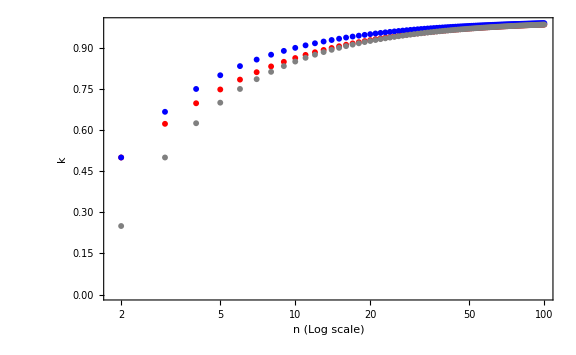

```mathematica
ListPlot[{Transpose[{Range[2,100],First[Transpose[tblkopt]]}],
Transpose[{Range[2,100],Map[(1-1/#)&,Range[2,100]]}],

Transpose[{Range[2,100],Map[(1-1.5/#)&,Range[2,100]]}]},Frame->True,PlotRange->All,ImageSize->Large,FrameLabel->{"n (Log scale)","k"},ScalingFunctions->{"Log",None},PlotStyle->{Red,Blue,Gray}]
```

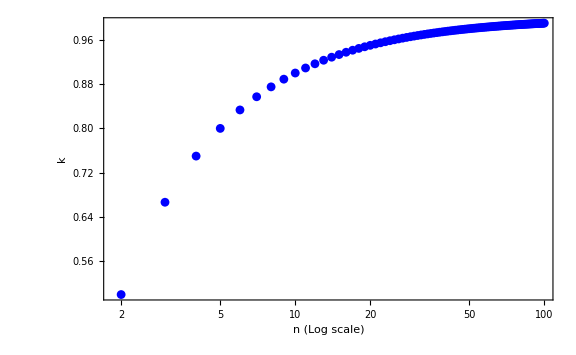

```mathematica
ListPlot[Transpose[{Range[2,100],Map[(1-1/#)&,Range[2,100]]}],Frame->True,PlotRange->All,ImageSize->Large,FrameLabel->{"n (Log scale)","k"},ScalingFunctions->{"Log",None},PlotStyle->Blue]
```

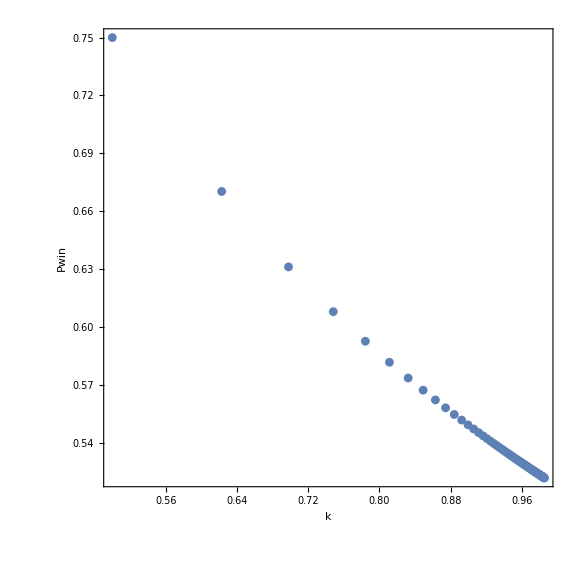

```mathematica
ListPlot[tblkopt,Frame->True,PlotRange->All,ImageSize->Large,FrameLabel->{"k","Pwin"},AspectRatio->1]
```

```mathematica
Timing[optpwk[1000]]
```

{1.40457,{0.998499,0.517796}}

```mathematica
Timing[optpwk[2000]]
```

{1.77598,{0.999249,0.517573}}

```mathematica
Timing[optpwk[5000]]
```

{5.91279,{0.999699,0.51744}}

```mathematica
Timing[optpwk[10000]]
```

{8.90646,{0.99985,0.517396}}

```mathematica
Map[N[(1-1.5/#)]&,{2,3,4,5,10,30,50,100,1000,2000,5000,10000}]
```

{0.25,0.5,0.625,0.7,0.85,0.95,0.97,0.985,0.9985,0.99925,0.9997,0.99985}

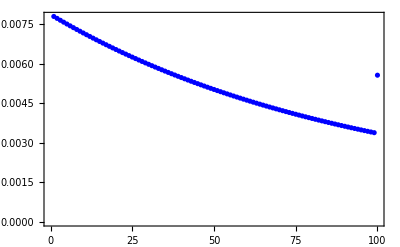

```mathematica
ListPlot[pwnrk[100,1-1.5/100],Frame->True,PlotRange->All,PlotStyle->Blue]
```

```mathematica
pwnrks[n_,r_,k_]:=1/(n-r+1)∏_(j=1)^(r-1) k⟦j⟧-∑_(i=1)^(r-1) (1/((n-r+i)(n-r+i+1))∏_(j=1)^(r-1) k⟦j⟧^If[i==j,n-r+1+i,If[i<j,1,0]])-1/n k⟦r⟧^n;
```

```mathematica
pnrks[n_,r_,k_]:={
1/(n-r+1)∏_(j=1)^(r-1) k⟦j⟧-∑_(i=1)^(r-1) (1/((n-r+i)(n-r+i+1))∏_(j=1)^(r-1) k⟦j⟧^If[i==j,n-r+1+i,If[i<j,1,0]])-1/n k⟦r⟧^n,
If[r<n,(n-r)/(n-r+1)∏_(j=1)^(r-1) k⟦j⟧-∑_(i=1)^(r-1) ((n-r)/((n-r+i)(n-r+i+1))∏_(j=1)^(r-1) k⟦j⟧^If[i==j,n-r+1+i,If[i<j,1,0]])-∏_(j=1)^r k⟦j⟧+∑_(i=1)^r ((n-r)/((n-r+i-1)(n-r+i))∏_(j=1)^r k⟦j⟧^If[i==j,n-r+i,If[i<j,1,0]]),If[k⟦r⟧==0,0]],
1/n k⟦r⟧^n
};
```

```mathematica
pwnkstbl[n_,k_]:=Table[pwnrks[n,r,k],{r,1,n}];
```

```mathematica
pwnkst[n_,k_]:=Total[Table[pwnrks[n,r,k],{r,1,n}]];
```

```mathematica
pwikt[n_,k_]:=Total[Table[pwnrks[n,r,Append[Table[k,{j,1,n-1}],0]],{r,1,n}]];
```

```mathematica
pwiknkt[n_,k_,nk_]:=Total[Table[pwnrks[n,r,Join[Table[k,{j,1,nk}],Table[0,{j,1,n-nk}]]],{r,1,n}]];
```

```mathematica
pwinn[n_]:=Total[Table[pwnrks[n,r,Append[Table[Subscript[k, j],{j,1,n-1}],0]],{r,1,n}]];
```

```mathematica
pwinmaxn[n_]:=Module[{vars,assumps},
vars=Table[Subscript[k, j],{j,1,n-1}];
assumps=Apply[And,Map[(0.5≤#<1)&,vars]];
NMaximize[{pwinn[n],assumps},vars,Reals]];
```

```mathematica
pwinmaxnkp[n_]:=Module[{pmax,ksmax},
{pmax,ksmax}=pwinmaxn[n];
{Map[Last,ksmax],pmax}];
```

```mathematica
pwinmaxnk[n_]:=Module[{pmax,ksmax},
{pmax,ksmax}=pwinmaxn[n];
Append[Map[Last,ksmax],0]];
```

```mathematica
TableForm[Table[pwinmaxnkp[n],{n,2,10}]]
```

0.5 | 0.75
0.672608
0.545532 | 0.679846
0.757467
0.692123
0.587554 | 0.64744
0.807606
0.767744
0.712357
0.622868 | 0.628888
0.840642
0.813796
0.779107
0.730858
0.652374 | 0.616904
0.864027
0.844724
0.820889
0.790119
0.747282
0.677259 | 0.608537
0.881443
0.866899
0.849495
0.828036
0.80035
0.761781
0.698501 | 0.602371
0.894912
0.883562
0.87029
0.854433
0.834902
0.809715
0.77461
0.716846 | 0.59764
0.905638
0.896534
0.886077
0.873868
0.859297
0.841364
0.818247
0.786015
0.732857 | 0.593897

```mathematica
newk100={0.9907522018170605,0.9906681326445045,0.9905830077860049,0.9904968043710631,0.9904095000453174,0.9903210709665161,0.9902314927833251,0.9901407396521342,0.9900487862915078,0.9899556052768766,0.9898611688726277,0.9897654478246417,0.9896684131429064,0.989570032901518,0.9894702763056411,0.9893691090124757,0.9892664974338905,0.9891624055815437,0.9890567972219049,0.9889496339612267,0.9888408752271814,0.9887304810990079,0.98861840718822,0.9885046101749426,0.9883890436434717,0.9882716585834819,0.9881524057576806,0.988031233675073,0.9879080850599743,0.9877829056145255,0.9876556351125245,0.9875262122805245,0.9873945707465108,0.9872606454721476,0.9871243669086815,0.9869856575591857,0.986844442437083,0.9867006396544284,0.9865541645549928,0.9864049274050987,0.9862528360968876,0.9860977907895049,0.9859396878970522,0.9857784177711911,0.9856138680844319,0.9854459150288922,0.9852744314858354,0.985099282220113,0.9849203231195287,0.9847374052989807,0.984550364343138,0.9843590335342786,0.9841632292262847,0.9839627580311077,0.9837574169030787,0.9835469841562214,0.9833312272702842,0.9831098952508172,0.9828827192385695,0.9826494110979409,0.9824096604745742,0.9821631352269778,0.9819094745035326,0.9816482886829001,0.9813791557219432,0.9811016170384314,0.980815174866105,0.980519285521403,0.9802133523929896,0.979896722255948,0.9795686775270424,0.9792284245997073,0.9788750854220505,0.9785076823864186,0.978125125350977,0.9777261922613983,0.9773095096067517,0.9768735193816581,0.976416451424152,0.975936280505687,0.9754306715699982,0.9748969195516408,0.9743318605806934,0.9737317620788893,0.9730921796511781,0.9724077610104946,0.9716719749711723,0.970876750098772,0.9700119216503755,0.969064461166302,0.9680172520525469,0.9668471945004676,0.9655220179466444,0.9639946040530442,0.9621922108979255,0.9599934535630766,0.9571718829258737,0.9532218071917358,0.9465410646364022,0};
```

```mathematica
pwnkstbl[100,newk100]
```

{0.00605084,0.00605192,0.00605283,0.00605359,0.00605418,0.00605459,0.00605484,0.00605492,0.00605483,0.00605455,0.0060541,0.00605346,0.00605264,0.00605163,0.00605043,0.00604904,0.00604745,0.00604567,0.00604368,0.00604148,0.00603908,0.00603646,0.00603363,0.00603058,0.00602731,0.00602381,0.00602008,0.00601612,0.00601192,0.00600747,0.00600278,0.00599783,0.00599263,0.00598717,0.00598144,0.00597544,0.00596916,0.0059626,0.00595575,0.0059486,0.00594115,0.00593339,0.00592532,0.00591693,0.0059082,0.00589914,0.00588974,0.00587997,0.00586985,0.00585935,0.00584847,0.00583719,0.00582552,0.00581343,0.00580091,0.00578795,0.00577454,0.00576066,0.0057463,0.00573145,0.00571609,0.00570019,0.00568375,0.00566674,0.00564914,0.00563093,0.00561209,0.00559259,0.0055724,0.0055515,0.00552986,0.00550744,0.00548421,0.00546013,0.00543515,0.00540924,0.00538234,0.0053544,0.00532536,0.00529516,0.00526372,0.00523097,0.00519681,0.00516116,0.00512388,0.00508487,0.00504397,0.00500102,0.00495581,0.00490813,0.00485768,0.00480413,0.00474705,0.00468592,0.00462,0.00454833,0.00446945,0.00438106,0.00427885,0.0041521}

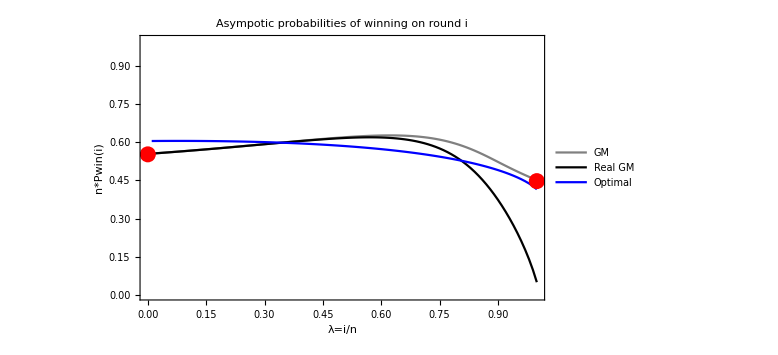

```mathematica
ListLinePlot[
{Last[pwtGMtblnP],
Transpose[{Range[100]/100,100pwnkstbl[100,getkGM[100]]}],
Transpose[{Range[100]/100,100pwnkstbl[100,newk100]}]},
Epilog->{
Red,PointSize[0.02],Point[{0,1-ⅇ^-c}],
Red,PointSize[0.02],Point[{1,ⅇ^-c}]},
Frame->True,PlotRange->{All,{0,1}},PlotLabel->"Asympotic probabilities of winning on round i",
FrameLabel->{"λ=i/n","n*Pwin(i)"},ImageSize->Large,PlotStyle->{Gray,Black,Blue},PlotLegends->{"GM","Real GM","Optimal"}]
```

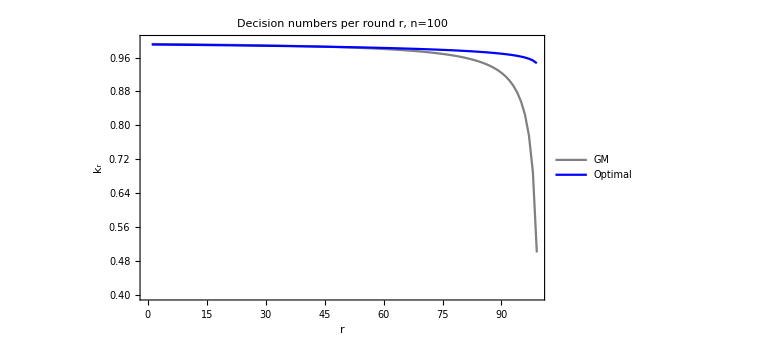

```mathematica
ListLinePlot[
{Transpose[{Range[99],Most[getkGM[100]]}],
Transpose[{Range[99],Most[newk100]}]},
Frame->True,PlotRange->{All,{0.4,1}},PlotLabel->"Decision numbers per round r, n=100",
FrameLabel->{"r","k_r"},ImageSize->Large,PlotStyle->{Gray,Blue},PlotLegends->{"GM","Optimal"}]
```

```mathematica
logdata100=Transpose[{Log[100-Range[99]],Most[newk100]}];
```

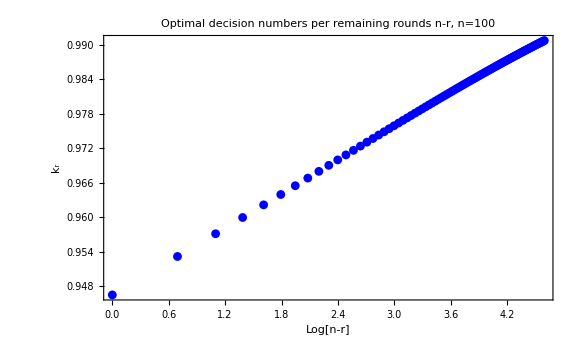

```mathematica
ListPlot[logdata100,Axes->True,AxesOrigin->{Log[51],1-1.5/100},
Frame->True,PlotRange->All,PlotLabel->"Optimal decision numbers per remaining rounds n-r, n=100",
FrameLabel->{"Log[n-r]","k_r"},ImageSize->Large,PlotStyle->{Blue}]
```

```mathematica
Timing[newk50=pwinmaxnk[50];]
```

{49.4325,Null}

```mathematica
logdata50=Transpose[{Log[50-Range[49]],Most[newk50]}];
```

```mathematica
Timing[newk20=pwinmaxnk[20];]
```

{1.63703,Null}

```mathematica
logdata20=Transpose[{Log[20-Range[19]],Most[newk20]}];
```

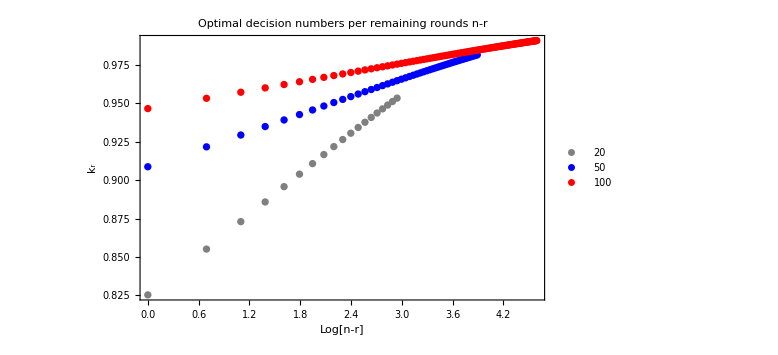

```mathematica
ListPlot[{logdata20,logdata50,logdata100},
Frame->True,PlotRange->All,PlotLabel->"Optimal decision numbers per remaining rounds n-r",
FrameLabel->{"Log[n-r]","k_r"},ImageSize->Large,PlotStyle->{Gray,Blue,Red},PlotLegends->{20,50,100}]
```

```mathematica
TableForm[Map[Fit[#,{1,x},x]&,{logdata20,logdata50,logdata100}]]
```

0.82537+0.0436991 x
0.909172+0.0187327 x
0.946981+0.00961046 x

```mathematica
Map[(1/#)&,{0.0436991,0.0187327,0.00961046}]
```

{22.8838,53.3826,104.053}

```mathematica
naivek[n_]:=Table[(j-1)/j,{j,n,1,-1}];
```

```mathematica
krn[n_,r_]:=(1-1/n)+(1/n)Log[(n-r)/n];
```

```mathematica
kapprox[n_]:=Append[Table[krn[n,r],{r,1,n-1}],0];
```

```mathematica
krn2[n_,r_]:=(1-1/n-Log[n]/n)+(1/n)Log[n-r];
```

```mathematica
tbl20=Table[{Log[20-r],krn[20,r]},{r,1,19}];tbl50=Table[{Log[50-r],krn[50,r]},{r,1,49}];tbl100=Table[{Log[100-r],krn[100,r]},{r,1,99}];
```

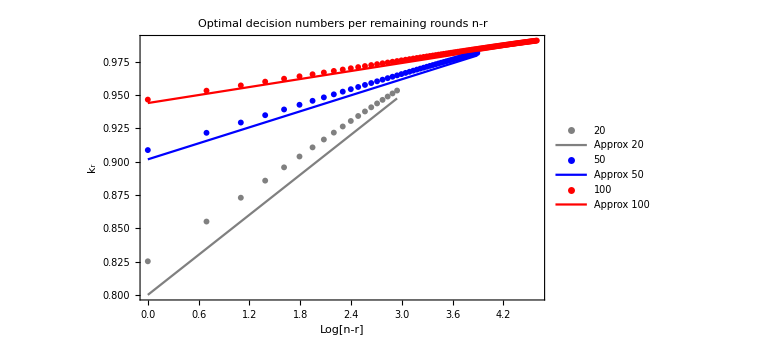

```mathematica
ListPlot[{logdata20,tbl20,logdata50,tbl50,logdata100,tbl100},Frame->True,PlotRange->All,ImageSize->Large,PlotLabel->"Optimal decision numbers per remaining rounds n-r",
FrameLabel->{"Log[n-r]","k_r"},PlotStyle->{Gray,Gray,Blue,Blue,Red,Red},Joined->{False,True,False,True,False,True},PlotLegends->{20,"Approx 20",50,"Approx 50",100,"Approx 100"}]
```

```mathematica
subseries[x_,y_]:=Transpose[{First[Transpose[x]],Last[Transpose[x]]-Last[Transpose[y]]}];
```

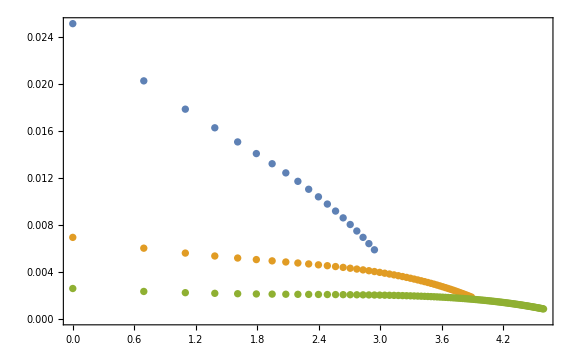

```mathematica
ListPlot[{subseries[logdata20,tbl20],subseries[logdata50,tbl50],subseries[logdata100,tbl100]},Frame->True,PlotRange->All,ImageSize->Large]
```

## 7. Simulation

Generate draws

```mathematica
nruns=1000000;
```

```mathematica
np=100;
```

```mathematica
tbl=RandomReal[{0,1},{nruns,np}];
```

```mathematica
big=tbl;
```

```mathematica
small=Take[tbl,100000];
```

Return win/loss and round

```mathematica
vmax[k_,a_]:=Module[{m,mp,mv,pg,v,fp},
m=Max[a];
mp=Ordering[a,-1]⟦1⟧;
mv=MapThread[(#1>#2)&,{a,k}];
pg=Position[mv,True]⟦1,1⟧;
v=Boole[First[Pick[a,mv]]==m];
fp=Boole[mp>pg];
{{v,fp,pg,mp},m}];
```

```mathematica
vmax[{2/3,1/2,0},{0.4,0.8,0.6}]
```

{{1,0,2,2},0.8}

```mathematica
vmax[{2/3,1/2,0},{0.7,0.8,0.6}]
```

{{0,1,1,2},0.8}

```mathematica
vmax[{2/3,1/2,0},{0.6,0.4,0.2}]
```

{{0,0,3,1},0.6}

```mathematica
evalk[k_,as_]:=Module[{asn},
asn=Map[Take[#,Length[k]]&,as];
Map[vmax[k,#]&,asn]];
```

```mathematica
tallyf[list_]:=Module[{tl,nr,tlf,tlfs},
tl=Tally[list,#1⟦1⟧===#2⟦1⟧&];
nr=Length[list];
tlf=Map[{#⟦1⟧⟦1⟧,N[#⟦2⟧/nr]}&,tl];
tlfs=Sort[tlf,(#1⟦2⟧>#2⟦2⟧)&];
tlfs];
```

```mathematica
meanmax[list_]:=N[Mean[Map[Last,list]]];
```

```mathematica
tallymax[list_]:=tallyf[Map[{Last[First[#]]}&,list]];
```

```mathematica
summax[list_]:=N[Mean[First[Transpose[Map[First,list]]]]];
```

```mathematica
tallysum[{{v_,fp_,pg_,mp_},m_}]:=If[fp==1,{v,fp,pg},{v,fp,mp}];
```

```mathematica
tsel[tlf_,indxj_]:=Module[{ans},ans=Select[tlf,#⟦1⟧==indxj&];If[ans≠{},ans⟦1,2⟧,ans]];
```

```mathematica
tallyfs[n_,list_]:=Module[{list2,tl,nr,tlf,indx,ordt,pordt},
list2=Map[tallysum,list];
tl=Tally[list2];
nr=Length[list2];
tlf=Map[{#⟦1⟧,N[#⟦2⟧/nr]}&,tl];
indx=Flatten[Append[Table[{{1,0,j},{0,1,j},{0,0,j}},{j,1,n-1}],{{1,0,n}}],1];
ordt=Table[{indx⟦j⟧,tsel[tlf,indx⟦j⟧]},{j,1,Length[indx]}];
pordt=Partition[ordt,3,3,{1,1},{}];
pordt];
```

```mathematica
getr[list_,r_]:=Select[list,(tallysum[#]⟦3⟧==r)&];
```

```mathematica
getrplus[list_,r_]:=Select[list,(tallysum[#]⟦3⟧>r)&];
```

n = 3, 5, 10: Basic

#### n=3

```mathematica
TableForm[N[{naivek[3],getkGM[3],pwinmaxnk[3]}]]
```

0.666667 | 0.5 | 0.
0.689898 | 0.5 | 0.
0.672608 | 0.545532 | 0.

```mathematica
Timing[
smplres3=evalk[naivek[3],big];
smplres3GM=evalk[getkGM[3],big];
smplres3New=evalk[pwinmaxnk[3],big];]
```

{68.6427,Null}

#### n=5

```mathematica
TableForm[N[{naivek[5],getkGM[5],pwinmaxnk[5]}]]
```

0.8 | 0.75 | 0.666667 | 0.5 | 0.
0.82459 | 0.775845 | 0.689898 | 0.5 | 0.
0.807606 | 0.767744 | 0.712357 | 0.622868 | 0.

```mathematica
Timing[
smplres5=evalk[naivek[5],big];
smplres5GM=evalk[getkGM[5],big];
smplres5New=evalk[pwinmaxnk[5],big];]
```

{74.4563,Null}

#### n=10

```mathematica
TableForm[N[{naivek[10],getkGM[10],pwinmaxnk[10]}]]
```

0.9 | 0.888889 | 0.875 | 0.857143 | 0.833333 | 0.8 | 0.75 | 0.666667 | 0.5 | 0.
0.916044 | 0.906265 | 0.89391 | 0.877807 | 0.855949 | 0.82459 | 0.775845 | 0.689898 | 0.5 | 0.
0.905638 | 0.896534 | 0.886077 | 0.873868 | 0.859297 | 0.841364 | 0.818247 | 0.786015 | 0.732857 | 0.

```mathematica
Timing[
smplres10=evalk[naivek[10],big];
smplres10GM=evalk[getkGM[10],big];
smplres10New=evalk[pwinmaxnk[10],big];]
```

{85.3591,Null}

#### Checking the distribution of the maximum along r

```mathematica
{TableForm[tallymax[smplres3]],TableForm[tallymax[smplres5]],TableForm[tallymax[smplres10]]}
```

{1 | 0.333931
2 | 0.333622
3 | 0.332447,5 | 0.20064
4 | 0.200192
1 | 0.199992
2 | 0.19969
3 | 0.199486,5 | 0.100517
6 | 0.100338
7 | 0.100323
9 | 0.100269
4 | 0.100133
10 | 0.099901
2 | 0.099878
1 | 0.099838
8 | 0.09943
3 | 0.099373}

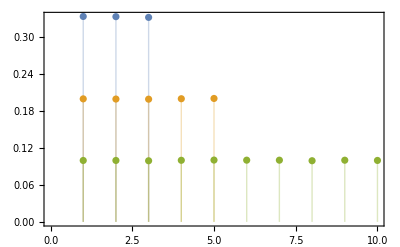

```mathematica
ListPlot[{tallymax[smplres3],tallymax[smplres5],tallymax[smplres10]},Frame->True,PlotRange->{All,{0,Automatic}},AxesOrigin->{0,0},Filling->Axis]
```

Checking the expected value of the maximum

```mathematica
TableForm[{{meanmax[smplres3],meanmax[smplres5],meanmax[smplres10]},N[{3/4,5/6,10/11}]}]
```

0.74969 | 0.833247 | 0.909148
0.75 | 0.833333 | 0.909091

n = 3, 5, 10: Checking probabilities per round and outcome

### n=3

#### 1 - 1/n

```mathematica
Map[TableForm,tallyfs[3,smplres3]]
```

{1
0
1 | 0.234868
0
1
1 | 0.098677
0
0
1 | 0.099063,1
0
2 | 0.242295
0
1
2 | 0.082281
0
0
2 | 0.041849,1
0
3 | 0.200967}

```mathematica
TableForm[Transpose[N[Table[pnrks[3,r,naivek[3]],{r,1,3}]]]]
```

0.234568 | 0.242284 | 0.201389
0.0987654 | 0.0825617 | 0.
0.0987654 | 0.0416667 | 0.

```mathematica
Total[Table[pnrks[3,r,naivek[3]],{r,1,3}],2]
```

1

```mathematica
{summax[smplres3],N[pwnkst[3,naivek[3]]]}
```

{0.67813,0.678241}

#### Original Paper

```mathematica
Map[TableForm,tallyfs[3,smplres3GM]]
```

{1
0
1 | 0.224201
0
1
1 | 0.085826
0
0
1 | 0.10973,1
0
2 | 0.248653
0
1
2 | 0.084852
0
0
2 | 0.041849,1
0
3 | 0.204889}

```mathematica
TableForm[Transpose[N[Table[pnrks[3,r,getkGM[3]],{r,1,3}]]]]
```

0.223879 | 0.248555 | 0.205126
0.0862231 | 0.0850959 | 0.
0.109454 | 0.0416667 | 0.

```mathematica
Total[Table[pnrks[3,r,getkGM[3]],{r,1,3}],2]
```

1.

```mathematica
{summax[smplres3GM],N[pwnkst[3,getkGM[3]]]}
```

{0.677743,0.67756}

#### New

```mathematica
Map[TableForm,tallyfs[3,smplres3New]]
```

{1
0
1 | 0.231359
0
1
1 | 0.095507
0
0
1 | 0.101493,1
0
2 | 0.231771
0
1
2 | 0.068943
0
0
2 | 0.054301,1
0
3 | 0.216626}

```mathematica
TableForm[Transpose[N[Table[pnrks[3,r,pwinmaxnk[3]],{r,1,3}]]]]
```

0.231904 | 0.231472 | 0.216471
0.0954882 | 0.0691187 | 0.
0.10143 | 0.0541176 | 0.

```mathematica
Total[Table[pnrks[3,r,pwinmaxnk[3]],{r,1,3}],2]
```

1.

```mathematica
{summax[smplres3New],N[pwnkst[3,pwinmaxnk[3]]]}
```

{0.679756,0.679846}

### n=5

#### 1 - 1/n

```mathematica
Map[TableForm,tallyfs[5,smplres5]]
```

{1
0
1 | 0.134723
0
1
1 | 0.065441
0
0
1 | 0.065269,1
0
2 | 0.136188
0
1
2 | 0.063357
0
0
2 | 0.047217,1
0
3 | 0.135674
0
1
3 | 0.058394
0
0
3 | 0.026442,1
0
4 | 0.127488
0
1
4 | 0.046448
0
0
4 | 0.006252,1
0
5 | 0.087107}

```mathematica
TableForm[Transpose[N[Table[pnrks[5,r,naivek[5]],{r,1,5}]]]]
```

0.134464 | 0.136155 | 0.136197 | 0.126921 | 0.0867695
0.065536 | 0.0632437 | 0.0587278 | 0.0464013 | 0.
0.065536 | 0.0474609 | 0.0263374 | 0.00625 | 0.

```mathematica
Total[Table[pnrks[5,r,naivek[5]],{r,1,5}],2]
```

1

```mathematica
{summax[smplres5],N[pwnkst[5,naivek[5]]]}
```

{0.62118,0.620507}

#### Original Paper

```mathematica
Map[TableForm,tallyfs[5,smplres5GM]]
```

{1
0
1 | 0.124078
0
1
1 | 0.05156
0
0
1 | 0.075914,1
0
2 | 0.130741
0
1
2 | 0.053422
0
0
2 | 0.05613,1
0
3 | 0.13761
0
1
3 | 0.054308
0
0
3 | 0.031283,1
0
4 | 0.136256
0
1
4 | 0.050222
0
0
4 | 0.006252,1
0
5 | 0.092224}

```mathematica
TableForm[Transpose[N[Table[pnrks[5,r,getkGM[5]],{r,1,5}]]]]
```

0.123754 | 0.130864 | 0.138047 | 0.13577 | 0.0918456
0.0516568 | 0.053344 | 0.0545693 | 0.0501742 | 0.
0.0762464 | 0.0562218 | 0.0312575 | 0.00625 | 0.

```mathematica
Total[Table[pnrks[5,r,getkGM[5]],{r,1,5}],2]
```

1.

```mathematica
{summax[smplres5GM],N[pwnkst[5,getkGM[5]]]}
```

{0.620909,0.62028}

#### New

```mathematica
Map[TableForm,tallyfs[5,smplres5New]]
```

{1
0
1 | 0.131591
0
1
1 | 0.061019
0
0
1 | 0.068401,1
0
2 | 0.131271
0
1
2 | 0.055848
0
0
2 | 0.053233,1
0
3 | 0.128928
0
1
3 | 0.04581
0
0
3 | 0.036772,1
0
4 | 0.124851
0
1
4 | 0.03052
0
0
4 | 0.018729,1
0
5 | 0.113027}

```mathematica
TableForm[Transpose[N[Table[pnrks[5,r,pwinmaxnk[5]],{r,1,5}]]]]
```

0.131289 | 0.131377 | 0.129437 | 0.124283 | 0.112502
0.061105 | 0.0557968 | 0.0461829 | 0.0305312 | 0.
0.0687114 | 0.0533471 | 0.0366875 | 0.0187504 | 0.

```mathematica
Total[Table[pnrks[5,r,pwinmaxnk[5]],{r,1,5}],2]
```

1.

```mathematica
{summax[smplres5New],N[pwnkst[5,pwinmaxnk[5]]]}
```

{0.629668,0.628888}

### n=10

#### 1 - 1/n

```mathematica
Map[TableForm,tallyfs[10,smplres10]]
```

{1
0
1 | 0.06498
0
1
1 | 0.035119
0
0
1 | 0.034858,1
0
2 | 0.065334
0
1
2 | 0.034587
0
0
2 | 0.030621,1
0
3 | 0.065106
0
1
3 | 0.034349
0
0
3 | 0.02613,1
0
4 | 0.065561
0
1
4 | 0.033943
0
0
4 | 0.021559,1
0
5 | 0.065324
0
1
5 | 0.033061
0
0
5 | 0.016242,1
0
6 | 0.063986
0
1
6 | 0.032592
0
0
6 | 0.010768,1
0
7 | 0.061132
0
1
7 | 0.03056
0
0
7 | 0.005618,1
0
8 | 0.054249
0
1
8 | 0.026087
0
0
8 | 0.001743,1
0
9 | 0.043121
0
1
9 | 0.017899
0
0
9 | 0.00011,1
0
10 | 0.025361}

```mathematica
TableForm[Transpose[N[Table[pnrks[10,r,naivek[10]],{r,1,10}]]]]
```

0.0651322 | 0.0653312 | 0.0654878 | 0.0654822 | 0.06508 | 0.0638286 | 0.0608677 | 0.0546623 | 0.0431188 | 0.0252658
0.0348678 | 0.0346431 | 0.0343517 | 0.0339451 | 0.0333223 | 0.032268 | 0.0303077 | 0.0263601 | 0.0179506 | 0.
0.0348678 | 0.0307946 | 0.0263076 | 0.0214058 | 0.0161506 | 0.0107374 | 0.00563135 | 0.00173415 | 0.0000976563 | 0.

```mathematica
Total[Table[pnrks[10,r,naivek[10]],{r,1,10}],2]
```

1

```mathematica
{summax[smplres10],N[pwnkst[10,naivek[10]]]}
```

{0.574154,0.574257}

#### Original Paper

```mathematica
Map[TableForm,tallyfs[10,smplres10GM]]
```

{1
0
1 | 0.058273
0
1
1 | 0.025732
0
0
1 | 0.041565,1
0
2 | 0.059759
0
1
2 | 0.02625
0
0
2 | 0.037282,1
0
3 | 0.060842
0
1
3 | 0.026466
0
0
3 | 0.03243,1
0
4 | 0.063005
0
1
4 | 0.027175
0
0
4 | 0.027293,1
0
5 | 0.064728
0
1
5 | 0.027782
0
0
5 | 0.02124,1
0
6 | 0.0657
0
1
6 | 0.028618
0
0
6 | 0.014452,1
0
7 | 0.065243
0
1
7 | 0.028634
0
0
7 | 0.007866,1
0
8 | 0.06055
0
1
8 | 0.026826
0
0
8 | 0.002419,1
0
9 | 0.049745
0
1
9 | 0.020836
0
0
9 | 0.00011,1
0
10 | 0.029179}

```mathematica
TableForm[Transpose[N[Table[pnrks[10,r,getkGM[10]],{r,1,10}]]]]
```

0.0583932 | 0.0597871 | 0.0613238 | 0.0629386 | 0.0644591 | 0.065471 | 0.0650166 | 0.0609988 | 0.0498162 | 0.0289473
0.0255626 | 0.026055 | 0.0266029 | 0.0272021 | 0.02782 | 0.0283437 | 0.0284322 | 0.027055 | 0.0209666 | 0.
0.0416068 | 0.0373726 | 0.032579 | 0.0271638 | 0.0211096 | 0.0145338 | 0.00790224 | 0.00244258 | 0.0000976563 | 0.

```mathematica
Total[Table[pnrks[10,r,getkGM[10]],{r,1,10}],2]
```

1.

```mathematica
{summax[smplres10GM],N[pwnkst[10,getkGM[10]]]}
```

{0.577024,0.577152}

#### New

```mathematica
Map[TableForm,tallyfs[10,smplres10New]]
```

{1
0
1 | 0.062812
0
1
1 | 0.031753
0
0
1 | 0.037026,1
0
2 | 0.062948
0
1
2 | 0.03078
0
0
2 | 0.033397,1
0
3 | 0.062386
0
1
3 | 0.02951
0
0
3 | 0.029678,1
0
4 | 0.062558
0
1
4 | 0.027916
0
0
4 | 0.026092,1
0
5 | 0.062119
0
1
5 | 0.025791
0
0
5 | 0.022063,1
0
6 | 0.060967
0
1
6 | 0.023267
0
0
6 | 0.017768,1
0
7 | 0.05966
0
1
7 | 0.019581
0
0
7 | 0.013317,1
0
8 | 0.056976
0
1
8 | 0.01522
0
0
8 | 0.008913,1
0
9 | 0.054237
0
1
9 | 0.009535
0
0
9 | 0.004544,1
0
10 | 0.049186}

```mathematica
TableForm[Transpose[N[Table[pnrks[10,r,pwinmaxnk[10]],{r,1,10}]]]]
```

0.0628852 | 0.0629544 | 0.062827 | 0.0624683 | 0.0618304 | 0.0608438 | 0.0594 | 0.0573133 | 0.0542176 | 0.0491572
0.0314766 | 0.0307298 | 0.0295672 | 0.0279433 | 0.0258014 | 0.0230648 | 0.0196174 | 0.0152564 | 0.00952922 | 0.
0.0371148 | 0.0335482 | 0.0298344 | 0.0259692 | 0.0219498 | 0.0177762 | 0.0134538 | 0.00900137 | 0.00446884 | 0.

```mathematica
Total[Table[pnrks[10,r,pwinmaxnk[10]],{r,1,10}],2]
```

1.

```mathematica
{summax[smplres10New],N[pwnkst[10,pwinmaxnk[10]]]}
```

{0.593849,0.593897}

### The second round

```mathematica
smplres3after1=getrplus[smplres3,1];
smplres5after1=getrplus[smplres5,1];
smplres10after1=getrplus[smplres10,1];
```

```mathematica
{TableForm[tallymax[smplres3after1]],TableForm[tallymax[smplres5after1]],TableForm[tallymax[smplres10after1]]}
```

{2 | 0.50079
3 | 0.49921,5 | 0.25067
4 | 0.250264
2 | 0.249678
3 | 0.249388,5 | 0.111725
9 | 0.111477
6 | 0.11143
7 | 0.111352
4 | 0.111273
10 | 0.110975
2 | 0.110925
8 | 0.110459
3 | 0.110384}

```mathematica
TableForm[{{Mean[Map[Max[Take[#,3]]&,big]],Mean[Map[Max[Take[#,5]]&,big]],Mean[Map[Max[Take[#,10]]&,big]]},N[{3/4,5/6,10/11}],{meanmax[smplres3],meanmax[smplres5],meanmax[smplres10]}}]
```

0.74969 | 0.833247 | 0.909148
0.75 | 0.833333 | 0.909091
0.74969 | 0.833247 | 0.909148

```mathematica
(* {{ccdfsn[3,1],cpdfsn[3,1],N[expmaxcpdfsn[3,1]]},{ccdfsn[5,1],cpdfsn[5,1],N[expmaxcpdfsn[5,1]]}} *)
```

```mathematica
TableForm[{{Mean[Map[Max[Rest[Take[#,3]]]&,big]],Mean[Map[Max[Rest[Take[#,5]]]&,big]],Mean[Map[Max[Rest[Take[#,10]]]&,big]]},N[{2/3,4/5,9/10}],{meanmax[smplres3after1],meanmax[smplres5after1],meanmax[smplres10after1]}}]
```

0.666262 | 0.7999 | 0.90006
0.666667 | 0.8 | 0.9
0.724098 | 0.823611 | 0.906659

n = 100

```mathematica
tblk100naive=N[naivek[100]];
tblk100GM=getkGM[100];
tblk100New=newk100;
tblk100approx=N[kapprox[100]];
```

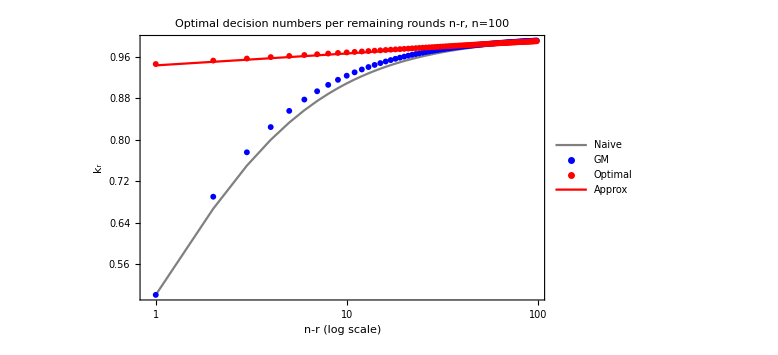

```mathematica
ListPlot[Map[Reverse[Most[#]]&,{naivek[100],getkGM[100],newk100,kapprox[100]}],Frame->True,PlotRange->All,ImageSize->Large,PlotStyle->{Gray,Blue,Red,Red},Joined->{True,False,False,True},PlotLegends->{"Naive","GM","Optimal","Approx"},ScalingFunctions->{"Log",None},FrameLabel->{"n-r (log scale)","k_r"},PlotLabel->"Optimal decision numbers per remaining rounds n-r, n=100"]
```

```mathematica
pred100naive=Transpose[N[Table[pnrks[100,r,naivek[100]],{r,1,100}]]];
pred100GM=Transpose[N[Table[pnrks[100,r,getkGM[100]],{r,1,100}]]];
pred100New=Transpose[N[Table[pnrks[100,r,newk100],{r,1,100}]]];
pred100Approx=Transpose[N[Table[pnrks[100,r,kapprox[100]],{r,1,100}]]];
```

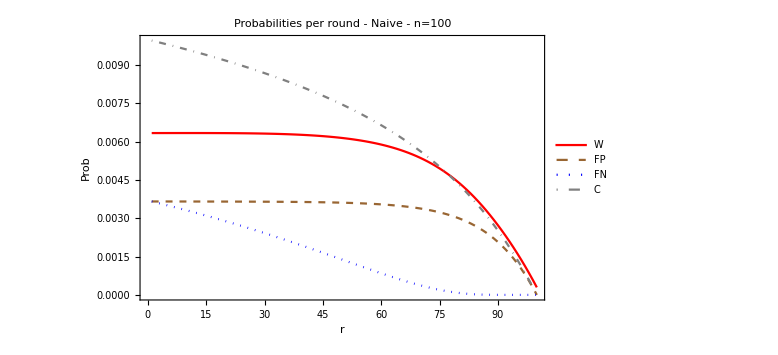

```mathematica
ListLinePlot[Append[pred100naive,(Most[1-Accumulate[Total[Transpose[pred100naive],{2}]]]/Range[99,1,-1])],Frame->True,PlotRange->All,PlotStyle->{Red,{Brown,Dashed},{Blue,Dotted},{Gray,DotDashed}},PlotLegends->{"W","FP","FN","C"},PlotLabel->"Probabilities per round - Naive - n=100",FrameLabel->{"r","Prob"},ImageSize->Large]
```

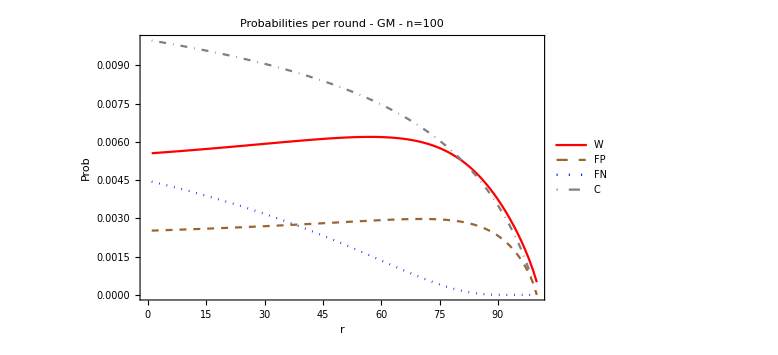

```mathematica
ListLinePlot[Append[pred100GM,(Most[1-Accumulate[Total[Transpose[pred100GM],{2}]]]/Range[99,1,-1])],Frame->True,PlotRange->All,PlotStyle->{Red,{Brown,Dashed},{Blue,Dotted},{Gray,DotDashed}},PlotLegends->{"W","FP","FN","C"},PlotLabel->"Probabilities per round - GM - n=100",FrameLabel->{"r","Prob"},ImageSize->Large]
```

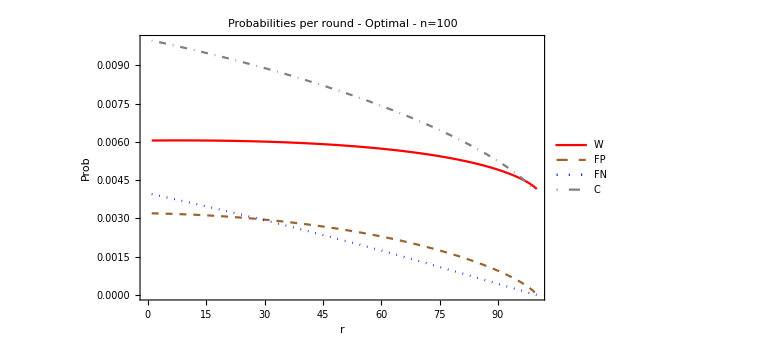

```mathematica
ListLinePlot[Append[pred100New,(Most[1-Accumulate[Total[Transpose[pred100New],{2}]]]/Range[99,1,-1])],Frame->True,PlotRange->All,PlotStyle->{Red,{Brown,Dashed},{Blue,Dotted},{Gray,DotDashed}},PlotLegends->{"W","FP","FN","C"},PlotLabel->"Probabilities per round - Optimal - n=100",FrameLabel->{"r","Prob"},ImageSize->Large]
```

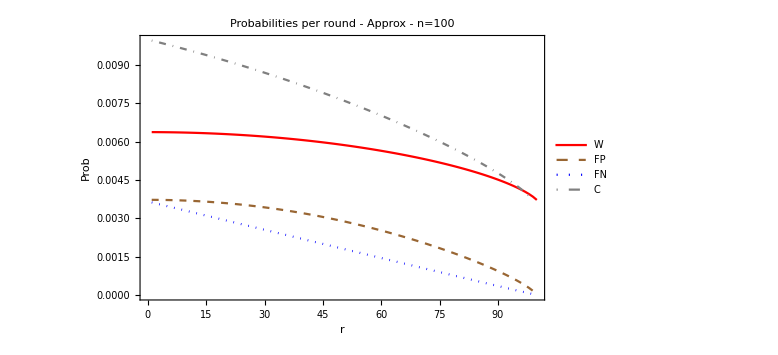

```mathematica
ListLinePlot[Append[pred100Approx,(Most[1-Accumulate[Total[Transpose[pred100Approx],{2}]]]/Range[99,1,-1])],Frame->True,PlotRange->All,PlotStyle->{Red,{Brown,Dashed},{Blue,Dotted},{Gray,DotDashed}},PlotLegends->{"W","FP","FN","C"},PlotLabel->"Probabilities per round - Approx - n=100",FrameLabel->{"r","Prob"},ImageSize->Large]
```

```mathematica
cumpw100=Map[Accumulate[#⟦1⟧]&,{pred100naive,pred100GM,pred100New,pred100Approx}];
```

```mathematica
Map[Ordering[#,-1]⟦1⟧&,Transpose[cumpw100]]
```

{4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,4,4,4,4,4,4,4,4,4,3,3,3,3,3}

```mathematica
Map[Length,Split[Map[Ordering[#,-1]⟦1⟧&,Transpose[cumpw100]]]]
```

{23,63,9,5}

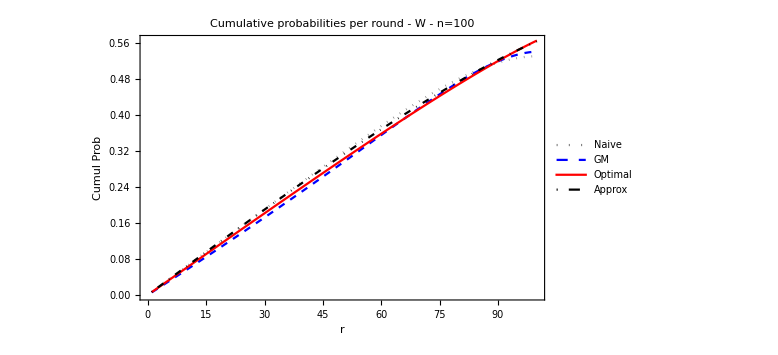

```mathematica
ListLinePlot[Map[Accumulate[#⟦1⟧]&,{pred100naive,pred100GM,pred100New,pred100Approx}],Frame->True,PlotRange->All,PlotStyle->{{Gray,Dotted},{Blue,Dashed},Red,{Black,DotDashed}},PlotLegends->{"Naive","GM","Optimal","Approx"},PlotLabel->"Cumulative probabilities per round - W - n=100",FrameLabel->{"r","Cumul Prob"},ImageSize->Large]
```

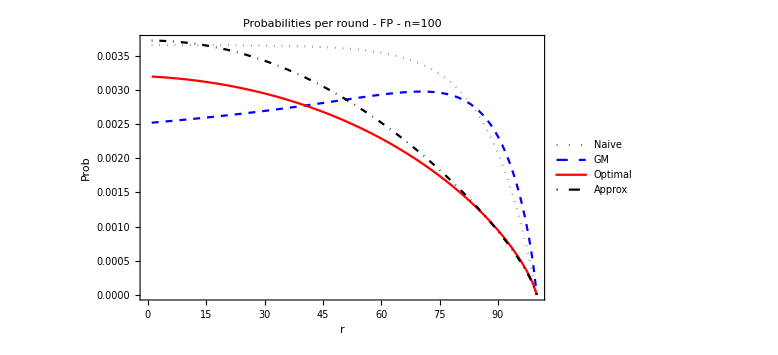

```mathematica
ListLinePlot[Map[#⟦2⟧&,{pred100naive,pred100GM,pred100New,pred100Approx}],Frame->True,PlotRange->All,PlotStyle->{{Gray,Dotted},{Blue,Dashed},Red,{Black,DotDashed}},PlotLegends->{"Naive","GM","Optimal","Approx"},PlotLabel->"Probabilities per round - FP - n=100",FrameLabel->{"r","Prob"},ImageSize->Large]
```

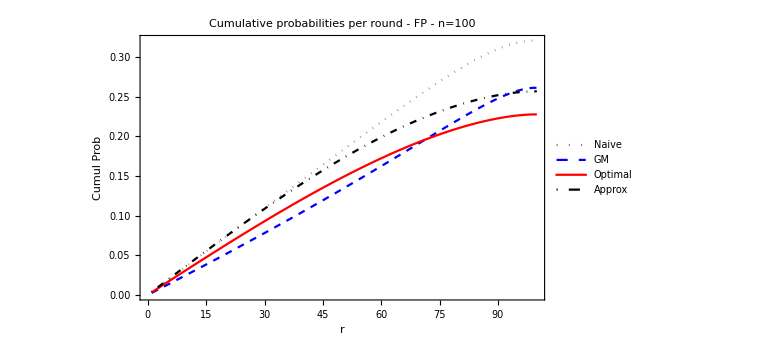

```mathematica
ListLinePlot[Map[Accumulate[#⟦2⟧]&,{pred100naive,pred100GM,pred100New,pred100Approx}],Frame->True,PlotRange->All,PlotStyle->{{Gray,Dotted},{Blue,Dashed},Red,{Black,DotDashed}},PlotLegends->{"Naive","GM","Optimal","Approx"},PlotLabel->"Cumulative probabilities per round - FP - n=100",FrameLabel->{"r","Cumul Prob"},ImageSize->Large]
```

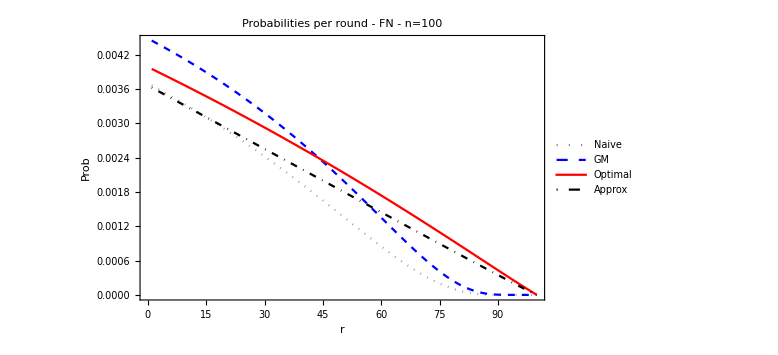

```mathematica
ListLinePlot[Map[#⟦3⟧&,{pred100naive,pred100GM,pred100New,pred100Approx}],Frame->True,PlotRange->All,PlotStyle->{{Gray,Dotted},{Blue,Dashed},Red,{Black,DotDashed}},PlotLegends->{"Naive","GM","Optimal","Approx"},PlotLabel->"Probabilities per round - FN - n=100",FrameLabel->{"r","Prob"},ImageSize->Large]
```

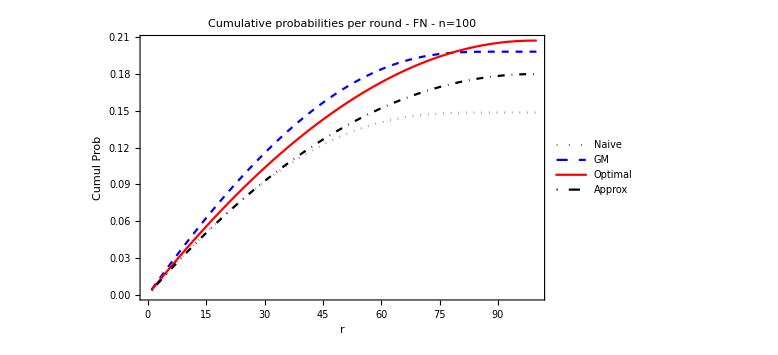

```mathematica
ListLinePlot[Map[Accumulate[#⟦3⟧]&,{pred100naive,pred100GM,pred100New,pred100Approx}],Frame->True,PlotRange->All,PlotStyle->{{Gray,Dotted},{Blue,Dashed},Red,{Black,DotDashed}},PlotLegends->{"Naive","GM","Optimal","Approx"},PlotLabel->"Cumulative probabilities per round - FN - n=100",FrameLabel->{"r","Cumul Prob"},ImageSize->Large]
```

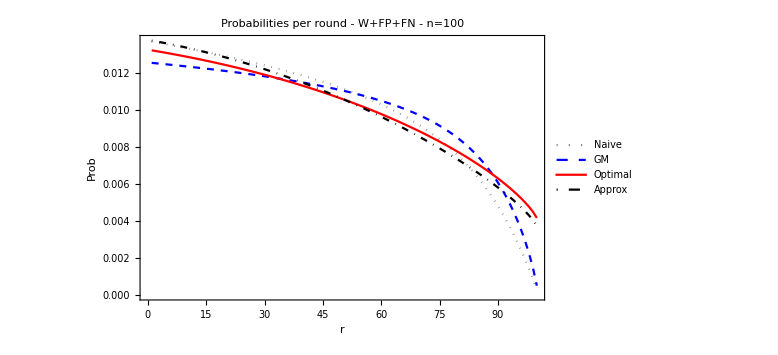

```mathematica
ListLinePlot[Map[Total[Transpose[#],{2}]&,{pred100naive,pred100GM,pred100New,pred100Approx}],Frame->True,PlotRange->All,PlotStyle->{{Gray,Dotted},{Blue,Dashed},Red,{Black,DotDashed}},PlotLegends->{"Naive","GM","Optimal","Approx"},PlotLabel->"Probabilities per round - W+FP+FN - n=100",FrameLabel->{"r","Prob"},ImageSize->Large]
```

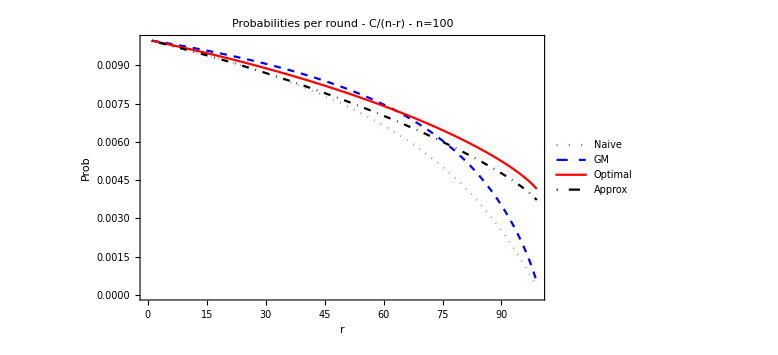

```mathematica
ListLinePlot[Map[(Most[1-Accumulate[Total[Transpose[#],{2}]]]/Range[99,1,-1])&,{pred100naive,pred100GM,pred100New,pred100Approx}],Frame->True,PlotRange->All,PlotStyle->{{Gray,Dotted},{Blue,Dashed},Red,{Black,DotDashed}},PlotLegends->{"Naive","GM","Optimal","Approx"},PlotLabel->"Probabilities per round - C/(n-r) - n=100",FrameLabel->{"r","Prob"},ImageSize->Large]
```

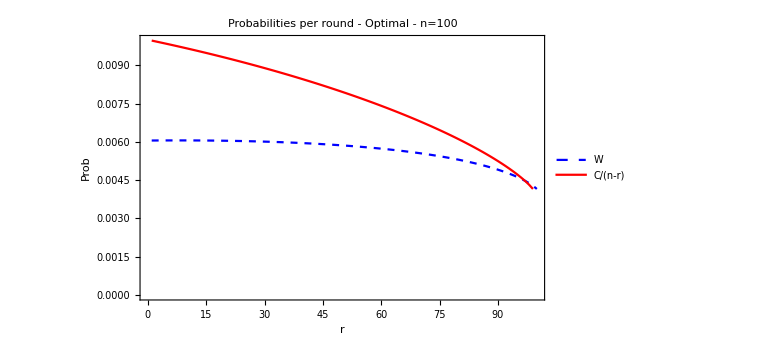

```mathematica
ListLinePlot[{pred100New⟦1⟧,(Most[1-Accumulate[Total[Transpose[pred100New],{2}]]]/Range[99,1,-1])},Frame->True,PlotRange->All,PlotStyle->{{Blue,Dashed},Red},PlotLegends->{"W","C/(n-r)"},PlotLabel->"Probabilities per round - Optimal - n=100",FrameLabel->{"r","Prob"},ImageSize->Large]
```

```mathematica
Timing[smplres100Naive=evalk[tblk100naive,big];]
```

{80.1471,Null}

```mathematica
Timing[smplres100GM=evalk[tblk100GM,big];]
```

{81.4071,Null}

```mathematica
Timing[smplres100New=evalk[tblk100New,big];]
```

{81.3761,Null}

```mathematica
Timing[smplres100Approx=evalk[tblk100approx,big];]
```

{80.2365,Null}

```mathematica
Map[Total[#⟦1⟧]&,{pred100naive,pred100GM,pred100New,pred100Approx}]
```

{0.530447,0.54053,0.56507,0.563211}

```mathematica
Map[summax,{smplres100Naive,smplres100GM,smplres100New,smplres100Approx}]
```

{0.530607,0.541101,0.565022,0.563432}

n = 200

```mathematica
tblk200naive=N[naivek[200]];
tblk200approx=N[kapprox[200]];
```

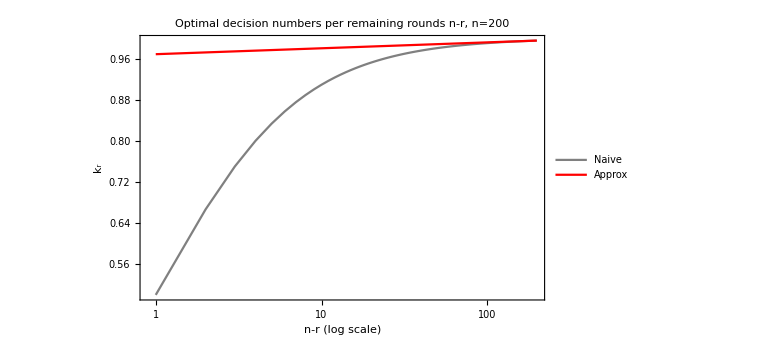

```mathematica
ListLinePlot[Map[Reverse[Most[#]]&,{tblk200naive,tblk200approx}],Frame->True,PlotRange->All,ImageSize->Large,PlotStyle->{Gray,Red},PlotLegends->{"Naive","Approx"},ScalingFunctions->{"Log",None},FrameLabel->{"n-r (log scale)","k_r"},PlotLabel->"Optimal decision numbers per remaining rounds n-r, n=200"]
```

```mathematica
Timing[pred200naive=Transpose[N[Table[pnrks[200,r,tblk200naive],{r,1,200}]]];]
```

{10.5713,Null}

```mathematica
Timing[pred200Approx=Transpose[N[Table[pnrks[200,r,tblk200approx],{r,1,200}]]];]
```

{10.7221,Null}

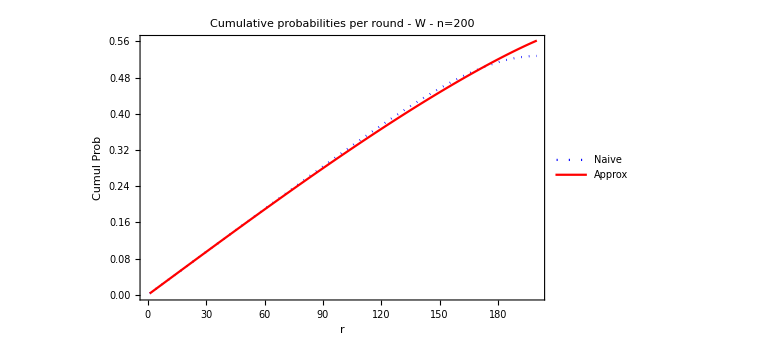

```mathematica
ListLinePlot[Map[Accumulate[#⟦1⟧]&,{pred200naive,pred200Approx}],Frame->True,PlotRange->All,PlotStyle->{{Blue,Dotted},Red},PlotLegends->{"Naive","Approx"},PlotLabel->"Cumulative probabilities per round - W - n=200",FrameLabel->{"r","Cumul Prob"},ImageSize->Large]
```

```mathematica
Map[Total[#⟦1⟧]&,{pred200naive,pred200Approx}]
```

{0.527956,0.56188}

n = 300

```mathematica
tblk300naive=N[naivek[300]];
tblk300approx=N[kapprox[300]];
```

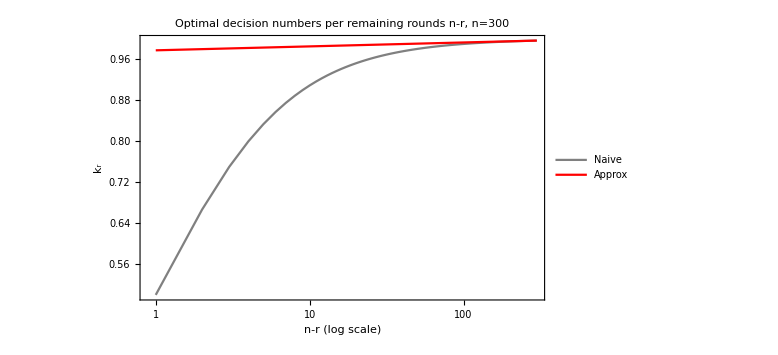

```mathematica
ListLinePlot[Map[Reverse[Most[#]]&,{tblk300naive,tblk300approx}],Frame->True,PlotRange->All,ImageSize->Large,PlotStyle->{Gray,Red},PlotLegends->{"Naive","Approx"},ScalingFunctions->{"Log",None},FrameLabel->{"n-r (log scale)","k_r"},PlotLabel->"Optimal decision numbers per remaining rounds n-r, n=300"]
```

```mathematica
Timing[pred300naive=Transpose[N[Table[pnrks[300,r,tblk300naive],{r,1,300}]]];]
```

{28.1081,Null}

```mathematica
Timing[pred300Approx=Transpose[N[Table[pnrks[300,r,tblk300approx],{r,1,300}]]];]
```

{28.1696,Null}

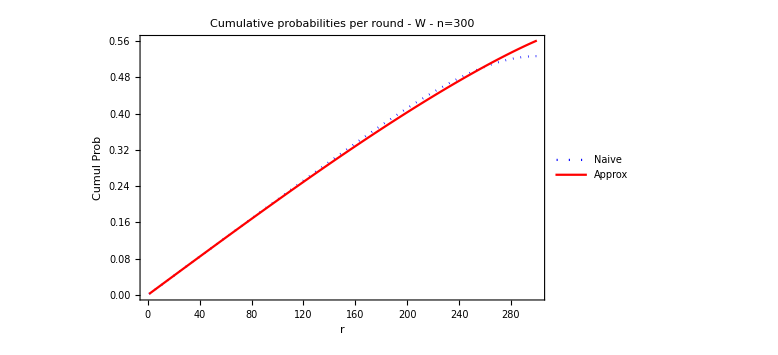

```mathematica
ListLinePlot[Map[Accumulate[#⟦1⟧]&,{pred300naive,pred300Approx}],Frame->True,PlotRange->All,PlotStyle->{{Blue,Dotted},Red},PlotLegends->{"Naive","Approx"},PlotLabel->"Cumulative probabilities per round - W - n=300",FrameLabel->{"r","Cumul Prob"},ImageSize->Large]
```

```mathematica
Map[Total[#⟦1⟧]&,{pred300naive,pred300Approx}]
```

{0.527124,0.561436}

n = 400

```mathematica
tblk400naive=N[naivek[400]];
tblk400approx=N[kapprox[400]];
```

```mathematica
Timing[pwnkst[400,tblk400naive]]
```

{22.3391,0.526708}

```mathematica
Timing[pwnkst[400,tblk400approx]]
```

{16.8102,0.561214}

n = 500

```mathematica
tblk500naive=N[naivek[500]];
tblk500approx=N[kapprox[500]];
```

```mathematica
Timing[pwnkst[100,tblk100approx]]
```

{0.447622,0.563211}

```mathematica
Timing[pwnkst[200,tblk200approx]]
```

{3.53315,0.56188}

```mathematica
Timing[pwnkst[300,tblk300approx]]
```

{9.37794,0.561436}

```mathematica
Timing[pwnkst[400,tblk400approx]]
```

{16.8102,0.561214}

```mathematica
Timing[pwnkst[500,tblk500naive]]
```

{43.1333,0.526458}

```mathematica
Timing[pwnkst[500,tblk500approx]]
```

{28.3107,0.561081}

n = 1000

```mathematica
tblk1000naive=N[naivek[1000]];
```

```mathematica
tblk1000approx=N[kapprox[1000]];
```

```mathematica
Timing[pwnkst[1000,tblk1000naive]]
```

{161.772,0.525959}

```mathematica
Timing[pwnkst[1000,tblk1000approx]]
```

{170.639,0.560814}

```mathematica
tbln1000=RandomReal[{0,1},{100000,1000}];
```

```mathematica
Timing[smplres1000Naive=evalk[tblk1000naive,tbln1000];]
```

{58.5294,Null}

```mathematica
Timing[smplres1000Approx=evalk[tblk1000approx,tbln1000];]
```

{59.9736,Null}

```mathematica
Map[summax,{smplres1000Naive,smplres1000Approx}]
```

{0.52472,0.55853}

n = 2000

```mathematica
tblk2000naive=N[naivek[2000]];
```

```mathematica
tblk2000approx=N[kapprox[2000]];
```

```mathematica
Timing[pwnkst[2000,tblk2000naive]]
```

{2207.03,0.525709}

```mathematica
Timing[pwnkst[2000,tblk2000approx]]
```

{2208.13,0.560681}

```mathematica
tbln2000=RandomReal[{0,1},{100000,2000}];
```

```mathematica
Timing[smplres2000Naive=evalk[tblk2000naive,tbln2000];]
```

{111.13,Null}

```mathematica
Timing[smplres2000Approx=evalk[tblk2000approx,tbln2000];]
```

{109.064,Null}

```mathematica
Map[summax,{smplres2000Naive,smplres2000Approx}]
```

{0.52388,0.55949}